## lecture des fichier de données

```mathematica
Needs["PlotLegends`"]
```

```mathematica
(* une fonction pratique pour convertir les nom de colonne Excel en entier *)
```

```mathematica
LX[l_]:=Switch[l,"A",1,"B",2,"C",3,"D",4,"E",5,"F",6,"G",7,"H",8,"I",9,"J",10,"K",11,"L",12,"M",13,"N",14,"O",15,"P",16,"Q",17,"R",18,"S",19,"T",20,"U",21,"V",22,"W",23,"X",24,"Y",25,"Z",26,"AA",27,"AB",28,"AC",29,"AD",30,"AE",31,"AF",32,"AG",33,"AH",34,"AI",35,"AJ",36,"AK",37,"AL",38,"AM",39,"AN",40,"AO",41,"AP",42,"AQ",43,"AR",44,"AS",45,"AT",46,"AU",47,"AV",48,"AW",49,"AX",50,"AY",51,"AZ",52,"BA",53,"BB",54,"BC",55,"BD",56,"BE",57,"BF",58,"BG",59,"BH",60,"BI",61]
```

```mathematica
(* fonction de base pour extraire des données a partir d'excel *)
```

```mathematica
TableExtract[sps_,col1_,row1_,col2_,row2_]:=Module[{nbrow=row2-row1+1,nbcol=col2-col1+1,res,i,j},
res=Table[Table[ 0,{i,1,nbcol}],{j,1,nbrow}];
Do[res[[j+1,i+1]]=sps[[row1+j,col1+i]],{i,0,nbcol-1},{j,0,nbrow-1}];
 res]
```

```mathematica
(* pour qu'une matrice ait l'air d'un vecteur, lorsque ce n'est qu'un vecteur *)
```

```mathematica
TableExtractF[sps_,col1_,row1_,col2_,row2_]:=Module[{tab=TableExtract[sps,col1,row1,col2,row2],i},
If[Length[tab[[1]]]==1,Table[tab[[i,1]],{i,1,Length[tab]}],tab]]
```

```mathematica
$MachineID
```

5100-90230-55947

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

/Users/croissantolivier/Documents

```mathematica
Directory[]
```

/Users/croissantolivier

PC du boulot

```mathematica
$MachineID
```

6202-75065-80383

```mathematica
SetDirectory["C:\\Users\\ocroissant\\Documents\\Projet X\\HMM_project"]
```

C:\Users\ocroissant\Documents\Projet X\HMM_project

PC de la Maison

```mathematica
$MachineID
```

6202-29516-23506

```mathematica
SetDirectory["C:/Users/olivier/Documents/Personel/Mathematica/Projet X"]
```

C:\Users\olivier\Documents\Personel\Mathematica\Projet X

```mathematica
If[($OperatingSystem=="Windows"),
Switch[$MachineID,
"6202-75065-80383",
MarketDataDirectory="C:\\Users\\ocroissant\\Documents\\Projet X\\HMM_project",
"6102-25062-85982",
MarketDataDirectory="C:\\Documents and Settings\\Olivier\\Documents\\My Bureau\\HMM_project",
"6239-65596-61921",
MarketDataDirectory="C:\\Users\\Olivier\\Documents\\HMM_project",
"6202-29516-23506",
MarketDataDirectory="C:/Users/olivier/Documents/Personel/Mathematica/Projet X"
],
Switch[$MachineID,
"5116-90412-58665",
MarketDataDirectory="/Users/croissantolivier/Documents/HMM_Project",
"5100-90230-55947",
MarketDataDirectory="/Users/olivier/Documents/HMM_Project"
]];
```

```mathematica
$MachineID
```

6202-75065-80383

```mathematica
MarketDataDirectory
```

C:\Users\ocroissant\Documents\Projet X\HMM_project

```mathematica
SetDirectory[MarketDataDirectory]
```

C:\Users\olivier\Documents\Personel\Mathematica\Projet X

```mathematica
FileNames[FileNameJoin[{"/Users/croissantolivier/Documents/HMM_Project","*"}]]
```

{/Users/croissantolivier/Documents/HMM_Project/.DS_Store,/Users/croissantolivier/Documents/HMM_Project/HMM.nb,/Users/croissantolivier/Documents/HMM_Project/SP_Vix_DailyPriceHistory.xls,/Users/croissantolivier/Documents/HMM_Project/vixcurrent.csv}

#### Import des données de SP_Vix _DailyPriceHistory

```mathematica
aa=Import["SP_Vix_DailyPriceHistory.xls"];
```

Import::nffil: File not found during Import.

```mathematica
Length[aa]
```

1

```mathematica
Length[aa[[1]]]
```

6724

```mathematica
aa[[1,6]]
```

{{1986,1,2,0,0,0.},N/A,N/A,209.59,N/A,N/A,N/A,N/A,18.07,N/A}

```mathematica
SPXbrut=TableExtractF[aa[[1]],LX["D"],6,LX["D"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 6 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 7 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 8 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
DateSPXbrut=TableExtractF[aa[[1]],LX["A"],6,LX["A"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 6 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 7 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 8 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
VIXbrut=TableExtractF[aa[[1]],LX["H"],1017,LX["H"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 1017 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 1018 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 1019 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
DateVIXbrut=TableExtractF[aa[[1]],LX["A"],1017,LX["A"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 1017 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 1018 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 1019 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
BXMbrut=TableExtractF[aa[[1]],LX["B"],130,LX["B"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 130 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 131 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 132 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
DateBXMbrut=TableExtractF[aa[[1]],LX["A"],130,LX["A"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 130 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 131 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 132 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
VXObrut=TableExtractF[aa[[1]],LX["I"],6,LX["I"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 6 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 7 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 8 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
DateVXObrut=TableExtractF[aa[[1]],LX["A"],6,LX["A"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 6 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 7 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 8 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
OVXbrut=TableExtractF[aa[[1]],LX["J"],5392,LX["J"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 5392 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 5393 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 5394 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
DateOVXbrut=TableExtractF[aa[[1]],LX["A"],5392,LX["A"],6711] ;
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partw: Part 5392 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 5393 of $Failed ⟦ 1 ⟧ does not exist.

Part::partw: Part 5394 of $Failed ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
VIX={};DateVIX={};
Do[If[NumberQ[VIXbrut[[i]]],
VIX=Append[VIX,VIXbrut[[i]]];
DateVIX=Append[DateVIX,DateVIXbrut[[i]]];i+=1;
],{i,1,Length[VIXbrut]}];
```

```mathematica
SPX={};DateSPX={};
Do[If[NumberQ[SPXbrut[[i]]],
SPX=Append[SPX,SPXbrut[[i]]];
DateSPX=Append[DateSPX,DateSPXbrut[[i]]];i+=1;
],{i,1,Length[SPXbrut]}];
```

```mathematica
BXM={};DateBXM={};
Do[If[NumberQ[BXMbrut[[i]]],
BXM=Append[BXM,BXMbrut[[i]]];
DateBXM=Append[DateBXM,DateBXMbrut[[i]]];i+=1;
],{i,1,Length[BXMbrut]}];
```

```mathematica
VXO={};DateVXO={};
Do[If[NumberQ[VXObrut[[i]]],
VXO=Append[VXO,VXObrut[[i]]];
DateVXO=Append[DateVXO,DateVXObrut[[i]]];i+=1;
],{i,1,Length[VXObrut]}];
```

```mathematica
OVX={};DateOVX={};
Do[If[NumberQ[OVXbrut[[i]]],
OVX=Append[OVX,OVXbrut[[i]]];
DateOVX=Append[DateOVX,DateOVXbrut[[i]]];i+=1;
],{i,1,Length[OVXbrut]}];
```

```mathematica
SPX[[1;;10]]
```

{209.59,210.88,210.65,213.8,207.97,206.11,205.96,206.72,206.64,208.26}

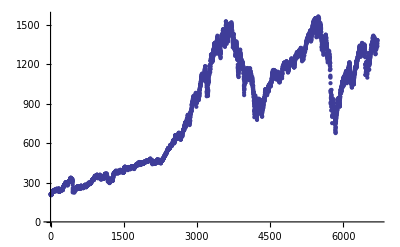

```mathematica
ListPlot[SPX]
```

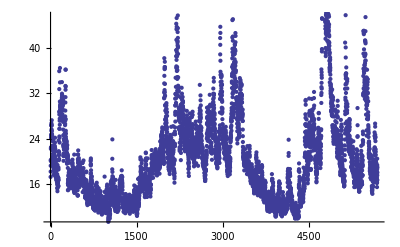

```mathematica
ListPlot[VIX]
```

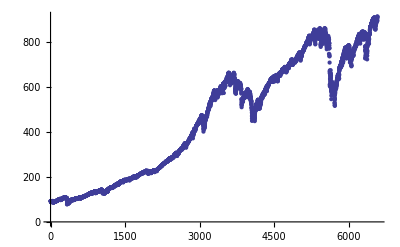

```mathematica
ListPlot[BXM]
```

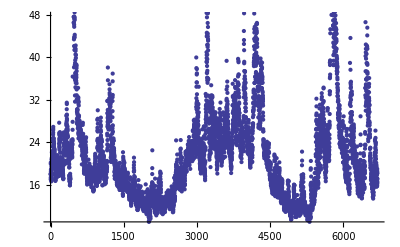

```mathematica
ListPlot[VXO]
```

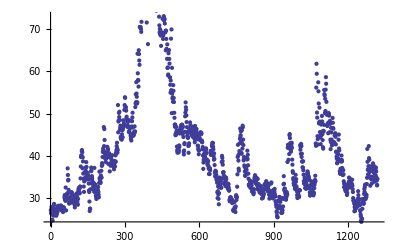

```mathematica
ListPlot[OVX]
```

Nombre de dimension cachées :  HiddenDimensionNb

Propabilité de transition du secteur caché : A[[i, j]]

probabilité initiale de la variable cachée : pi[[i]]

Probabilité d' observation Conditionellement a un etat caché : p[i, xt, theta]

#### Import des données de Datas Normalized

```mathematica
bb=Import["Datas_Normalized2.xls"];
```

```mathematica
DataBrut=Table[0,{i,1,20}];
```

```mathematica
DataBrut[[1]]={"EUR,SX5E","SX5E",TableExtractF[bb[[1]],LX["B"],4,LX["C"],3856] };
DataBrut[[2]]={"EUR VIX","V2X",TableExtractF[bb[[1]],LX["E"],4,LX["F"],3856] };
DataBrut[[3]]={"US SPX500","SPXT",TableExtractF[bb[[1]],LX["H"],4,LX["I"],3856] };
DataBrut[[4]]={"US,VIX","VIX",TableExtractF[bb[[1]],LX["K"],4,LX["L"],3856] };
DataBrut[[5]]={"GSCI Petrole","SPGSCLTR",TableExtractF[bb[[1]],LX["N"],4,LX["O"],3856] };
DataBrut[[6]]={"GSCI Or","SPGSGCTR",TableExtractF[bb[[1]],LX["Q"],4,LX["R"],3856] };
DataBrut[[7]]={"EUR/USD","EURUSD",TableExtractF[bb[[1]],LX["T"],4,LX["U"],3856] };
DataBrut[[8]]={"JPY/EUR","JPYEUR",TableExtractF[bb[[1]],LX["W"],4,LX["X"],3856] };
DataBrut[[9]]={"EUR Tenor 1Y","EUSA1",TableExtractF[bb[[1]],LX["Z"],4,LX["AA"],3856] };
DataBrut[[10]]={"EUR Tenor 2Y","EUSA2",TableExtractF[bb[[1]],LX["AC"],4,LX["AD"],3856] };
DataBrut[[11]]={"EUR Tenor 5Y","EUSA5",TableExtractF[bb[[1]],LX["AF"],4,LX["AG"],3856] };
DataBrut[[12]]={"EUR Tenor 10Y","EUSA10",TableExtractF[bb[[1]],LX["AI"],4,LX["AJ"],3856] };
DataBrut[[13]]={"US Tenor 1Y","USSW1",TableExtractF[bb[[1]],LX["AL"],4,LX["AM"],3856] };
DataBrut[[14]]={"US Tenor 2Y","USSW2",TableExtractF[bb[[1]],LX["AO"],4,LX["AP"],3856] };
DataBrut[[15]]={"US Tenor 5Y","USSW5",TableExtractF[bb[[1]],LX["AR"],4,LX["AS"],3856] };
DataBrut[[16]]={"US Tenor 10Y","USSW10",TableExtractF[bb[[1]],LX["AU"],4,LX["AV"],3856] };
DataBrut[[17]]={"ITraXX Main","ITRXEBE",TableExtractF[bb[[1]],LX["AX"],4,LX["AY"],2429] };
DataBrut[[18]]={"ITraXX Cross Over","ITRXEXE",TableExtractF[bb[[1]],LX["BA"],4,LX["BB"],2429] };
DataBrut[[19]]={"ITraXX Main USD","ITRXX",TableExtractF[bb[[1]],LX["BD"],4,LX["BE"],2598] };
DataBrut[[20]]={"ItraXX HY USD","IBOXHYSE",TableExtractF[bb[[1]],LX["BG"],4,LX["BH"],1218] };
```

```mathematica
DataBrut[[20,2]]==
```

IBOXHYSE

```mathematica
GetHistory[ticker_]:=Switch[ticker,
DataBrut[[1,2]], Transpose[DataBrut[[1,3]]][[2]],
DataBrut[[2,2]], Transpose[DataBrut[[2,3]]][[2]],
DataBrut[[3,2]], Transpose[DataBrut[[3,3]]][[2]],
DataBrut[[4,2]], Transpose[DataBrut[[4,3]]][[2]],
DataBrut[[5,2]], Transpose[DataBrut[[5,3]]][[2]],
DataBrut[[6,2]], Transpose[DataBrut[[6,3]]][[2]],
DataBrut[[7,2]], Transpose[DataBrut[[7,3]]][[2]],
DataBrut[[8,2]], Transpose[DataBrut[[8,3]]][[2]],
DataBrut[[9,2]], Transpose[DataBrut[[9,3]]][[2]],
DataBrut[[10,2]], Transpose[DataBrut[[10,3]]][[2]],
DataBrut[[11,2]], Transpose[DataBrut[[11,3]]][[2]],
DataBrut[[12,2]], Transpose[DataBrut[[12,3]]][[2]],
DataBrut[[13,2]], Transpose[DataBrut[[13,3]]][[2]],
DataBrut[[14,2]], Transpose[DataBrut[[14,3]]][[2]],
DataBrut[[15,2]], Transpose[DataBrut[[15,3]]][[2]],
DataBrut[[16,2]], Transpose[DataBrut[[16,3]]][[2]],
DataBrut[[17,2]], Transpose[DataBrut[[17,3]]][[2]],
DataBrut[[18,2]], Transpose[DataBrut[[18,3]]][[2]],
DataBrut[[19,2]], Transpose[DataBrut[[19,3]]][[2]],
DataBrut[[20,2]], Transpose[DataBrut[[20,3]]][[2]]
]
```

```mathematica
GetHistory["ITRXEBE"];
```

```mathematica
GetHistory[ticker1_,n_Integer]:=Module[{h1=GetHistory[ticker1],l1,l},
l1=Length[h1];l=Min[l1,n];Reverse[h1[[1;;l]]]]
```

```mathematica
GetHistory[ticker1_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],q1,q2,l},
l=Length[h1];q1=Min[l,n+p];q2=Min[l,p+1];Reverse[h1[[q2;;q1]]]]
```

```mathematica
GetHistory[ticker1_,ticker2_]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,l},
l1=Length[h1];l2=Length[h2];l=Min[l1,l2];Transpose[{h1[[1;;l]],h2[[1;;l]]}]]
```

```mathematica
GetHistory[ticker1_,ticker2_,n_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,l},
l1=Length[h1];l2=Length[h2];l=Min[l1,l2,n];Reverse[Transpose[{h1[[1;;l]],h2[[1;;l]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,q1,q2},
l1=Length[h1];l2=Length[h2];q1=Min[l1,l2,n+p];q2=Min[l1,l2,p+1];Reverse[Transpose[{h1[[q2;;q1]],h2[[q2;;q1]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,ticker3_,n_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],h3=GetHistory[ticker3],l1,l2,l3,l},
l1=Length[h1];l2=Length[h2];l3=Length[h3];l=Min[l1,l2,l3,n];Reverse[Transpose[{h1[[1;;l]],h2[[1;;l]],h3[[1;;l]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,ticker3_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],h3=GetHistory[ticker3],l1,l2,l3,q1,q2,},
l1=Length[h1];l2=Length[h2];l3=Length[h3];q1=Min[l1,l2,l3,n+p];q2=Min[l1,l2,l3,p+1];Reverse[Transpose[{h1[[q2;;q1]],h2[[q2;;q1]],h3[[q2;;q1]]}]]]
```

```mathematica
GetHistory["ITRXEBE",20]
```

{96.912,97.422,98.022,94.083,94.133,93.41,89.174,99.467,100.014,97.505,97.759,99.427,102.294,103.884,98.75,98.747,100.706,97.055,98.008,100.628}

```mathematica
GetHistory["ITRXEBE",10,10]
```

{96.912,97.422,98.022,94.083,94.133,93.41,89.174,99.467,100.014,97.505}

```mathematica
GetHistory["ITRXEBE","ITRXX",20]
```

{{96.912,76.042},{97.422,77.712},{98.022,77.056},{94.083,74.753},{94.133,73.024},{93.41,69.49},{89.174,69.896},{99.467,79.988},{100.014,80.325},{97.505,78.875},{97.759,79.701},{99.427,79.638},{102.294,80.897},{103.884,82.07},{98.75,79.738},{98.747,79.661},{100.706,80.9},{97.055,79.415},{98.008,82.517},{100.628,84.517}}

```mathematica
GetHistory["ITRXEBE","ITRXX",10,10]
```

{{96.912,76.042},{97.422,77.712},{98.022,77.056},{94.083,74.753},{94.133,73.024},{93.41,69.49},{89.174,69.896},{99.467,79.988},{100.014,80.325},{97.505,78.875}}

```mathematica
GetHistory["ITRXEBE","ITRXX","SPXT",20]
```

{{110.994,86.369,2660.7},{118.318,90.15,2630.05},{115.432,88.459,2657.76},{117.759,89.619,2659.55},{118.292,89.913,2655.84},{116.168,89.408,2670.85},{116.298,89.464,2669.37},{113.551,87.265,2673.77},{111.674,86.113,2676.6},{110.715,85.952,2678.77},{112.934,86.76,2676.21},{112.907,86.72,2676.21},{110.861,85.197,2696.26},{111.056,87.6,2662.94},{114.518,88.39,2646.75},{112.931,86.353,2670.36},{113.573,90.217,2621.46},{122.529,89.526,2637.89},{116.984,87.272,2672.11},{116.292,88.033,2669.92}}

```mathematica
GetHistory["ITRXEBE","ITRXX","SPXT",10,10]
```

{{110.994,86.369,2660.7},{118.318,90.15,2630.05},{115.432,88.459,2657.76},{117.759,89.619,2659.55},{118.292,89.913,2655.84},{116.168,89.408,2670.85},{116.298,89.464,2669.37},{113.551,87.265,2673.77},{111.674,86.113,2676.6},{110.715,85.952,2678.77}}

## Fonctions auxiliaires

```mathematica
InitialHiddenSateParameters2[TwoDimObservedThreeDimHidden]=Function[{x,NbStates},Module[{Ve,Vx1,Vx2},Ve=Table[1./(2 (NbStates-1))+1/2 KroneckerDelta[i,j],{i,1,NbStates},{j,1,NbStates}];Vx1=Table[1./(2 NbStates NbStates NbStates)+1/2 KroneckerDelta[j,k],{i,1,NbStates},{j,1,NbStates},{k,1,NbStates}];Vx2=Table[1./(2 NbStates NbStates NbStates)+1/2 KroneckerDelta[j,k],{i,1,NbStates},{j,1,NbStates},{k,1,NbStates}];{Ve,Vx1,Vx2}]];
```

## Fonctions Specifiques

### Fonctions auxiliaires

```mathematica
biSymetricToFlatIndex[i1_,j1_,n_]:=Module[{i,j},If[i1>=j1,i=i1;j=j1,i=j1;j=i1];If[i>2,Sum[k,{k,1,i-2}]+j,j]]
```

```mathematica
FlatToSymetricIndex[k_,n_]:=Module[{eps=k,i=1,j=1},While[eps>(i-1),eps=eps-(i-1);i=i+1];j=eps;{i,j}]
```

```mathematica
Module[{n=3},Do[Do[Print[biSymetricToFlatIndex[i,j,n]],{j,1,i-1}],{i,1,n}]]
```

1

2

3

```mathematica
Module[{n=3,k},Do[Do[k=biSymetricToFlatIndex[i,j,n];
Print[{i,j}," k=",k," => ",FlatToSymetricIndex[k,n]],{j,1,i-1}],{i,1,n}]]
```

{2,1} k=1 => {2,1}

{3,1} k=2 => {3,1}

{3,2} k=3 => {3,2}

### Densité gaussiennes

```mathematica
SPX[[2;;10]]
```

{210.88,210.65,213.8,207.97,206.11,205.96,206.72,206.64,208.26}

```mathematica
PDF[MultinormalDistribution[{μ1,μ2,μ3},{{σ1^2,ρ12 σ1 σ2,ρ13 σ1 σ3},{ρ12 σ1 σ2,σ2^2,ρ23 σ2 σ3},{ρ13 σ1 σ3,ρ23 σ2 σ3,σ3^2}}],{x1,x2,x3}]
```

ⅇ^(1/2 (-((x3-μ3) (-x3 σ1 σ2+μ3 σ1 σ2+x3 ρ12^2 σ1 σ2-μ3 ρ12^2 σ1 σ2-x2 ρ12 ρ13 σ1 σ3+μ2 ρ12 ρ13 σ1 σ3+x2 ρ23 σ1 σ3-μ2 ρ23 σ1 σ3+x1 ρ13 σ2 σ3-μ1 ρ13 σ2 σ3-x1 ρ12 ρ23 σ2 σ3+μ1 ρ12 ρ23 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1 σ2 σ3^2)-((x2-μ2) (-x3 ρ12 ρ13 σ1 σ2+μ3 ρ12 ρ13 σ1 σ2+x3 ρ23 σ1 σ2-μ3 ρ23 σ1 σ2-x2 σ1 σ3+μ2 σ1 σ3+x2 ρ13^2 σ1 σ3-μ2 ρ13^2 σ1 σ3+x1 ρ12 σ2 σ3-μ1 ρ12 σ2 σ3-x1 ρ13 ρ23 σ2 σ3+μ1 ρ13 ρ23 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1 σ2^2 σ3)-((x1-μ1) (x3 ρ13 σ1 σ2-μ3 ρ13 σ1 σ2-x3 ρ12 ρ23 σ1 σ2+μ3 ρ12 ρ23 σ1 σ2+x2 ρ12 σ1 σ3-μ2 ρ12 σ1 σ3-x2 ρ13 ρ23 σ1 σ3+μ2 ρ13 ρ23 σ1 σ3-x1 σ2 σ3+μ1 σ2 σ3+x1 ρ23^2 σ2 σ3-μ1 ρ23^2 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1^2 σ2 σ3)))/(2 √2 π^(3/2) √(σ1 σ2 σ3 (σ1 σ2 σ3-ρ12^2 σ1 σ2 σ3-ρ13^2 σ1 σ2 σ3+2 ρ12 ρ13 ρ23 σ1 σ2 σ3-ρ23^2 σ1 σ2 σ3)))

```mathematica
3
```

```mathematica
NormDens[x0_,σ_,x_]:=(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
LogNormDens[x0_,σ_,x_]:=-(x-x0)^2/(2 σ^2)-Log[√(2 π) σ]
```

```mathematica
BivariateNormDens[x_,y_,μ1_,μ2_,σ1_,σ2_,ρ_]:=If[ρ==1 && (μ1-x)/σ1==(μ2-y)/σ2,NormDens[μ1,σ1,x],If[ρ≠1,ExpR[(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ)/(2 (1-ρ^2))]/(2 π √(1- ρ^2)σ1 σ2),0]]
```

```mathematica
LogBivariateNormDens[x_,y_,μ1_,μ2_,σ1_,σ2_,ρ_]:=
If[ρ≠1 &&ρ≠-1,(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ)/(2 (1-ρ^2))-Log[2 π σ1 σ2 √(1- ρ^2)],
If[ρ==1 && (μ1-x)/σ1==(μ2-y)/σ2,LogNormDens[μ1,σ1,x],
If[ρ==-1 && (μ1-x)/σ1==(μ2-y)/σ2,LogNormDens[μ1,σ1,x],0]]]
```

```mathematica
TrivariateNormDens[x_,y_,z_,μ1_,μ2_,μ3_,σ1_,σ2_,σ3_,ρ12_,ρ13_,ρ23_]:=
If[ρ12==1 && (μ1-x)/σ1==(μ2-y)/σ2,BivariateNormDens[x,z,μ1,μ3,σ1,σ3,ρ13],
If[ρ13==1 && (μ1-x)/σ1==(μ3-y)/σ3,BivariateNormDens[x,y,μ1,μ2,σ1,σ2,ρ12],
If[ρ12≠1&& ρ13≠1,ExpR[(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ12)/(2 (1-ρ12^2))]/(2 π √(1- ρ12^2)σ1 σ2),0]]]
```

```mathematica
MultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim=Length[μ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
PDF[MultinormalDistribution[μ,Σ],x]]
```

```mathematica
LogMultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim=Length[μ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
Log[PDF[MultinormalDistribution[μ,Σ],x]]]
```

```mathematica
MultivariateΣ[σ_,ρ_]:=Module[{NbDim=Length[σ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}]]
```

```mathematica
MultivariateΣ[{σ1,σ2,σ3},{ρ1,ρ2,ρ3}]//MatrixForm
```

(σ1^2 | ρ1 σ1 σ2 | ρ2 σ1 σ3
ρ1 σ1 σ2 | σ2^2 | ρ3 σ2 σ3
ρ2 σ1 σ3 | ρ3 σ2 σ3 | σ3^2)

```mathematica
Eigenvalues[MultivariateΣ[{0.2,0.3,0.4},{0.3,0.3,0.4},{0.05,-0.05,0.05}]]
```

{0.166554,0.105,0.0684465}

```mathematica
LogMultivariateNormDens[{0.2,0.3,0.4},{0.3,0.3,0.4},{0.05,-0.05,0.05},{0.05,-0.05,0.05}]
```

-0.561616

```mathematica
LogMultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim,Σ},
NbDim=Length[μ];
Σ=Table[If[i==j,σ[[i]]*σ[[i]],ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
-0.5((Inverse[Σ].(x-μ)).(x-μ)+Log[Det[Σ]]+Length[Σ]1.837877066409345)]
```

### ExpR, LogR, LogSumExpR , MNormalize, FNormalize

```mathematica
LogR[a_]:=If[a==0, -1.23456789 10^99, Log[a]]
```

```mathematica
Attributes[LogR]={Listable}
```

{Listable}

```mathematica
ExpR[a_]:=If[a<-10^(3),0.,Exp[a]]
```

```mathematica
Attributes[ExpR]={Listable}
```

{Listable}

```mathematica
LogSumExp1[vec_]:=Log[Plus@@(Exp[vec])]
```

```mathematica
LogSumExp[vec_]:=Module[{biggest=Max[vec],vecp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=Sum[If[vecp[[i]]<logCutoff,0.0,ExpR[vecp[[i]]]],{i,1,Length[vec]}];
LogR[sum]+biggest]
```

```mathematica
LogSumExp2[vec_]:=Module[{biggest=Max[vec],vecp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=Sum[If[vecp[[i,j]]<logCutoff,0.0,ExpR[vecp[[i,j]]]],{i,1,Length[vec]},{j,1,Length[vec]}];LogR[sum]+biggest]
```

```mathematica
LogSumExp[{-1.25,-25,-3000000,-2}]
```

-0.863129

```mathematica
LogSumExp3[{-1.25,-25.,-3000000,-2}]
```

-0.863129

```mathematica
LogSumExpAux[vec_]:=Module[{biggest=Max[vec],vecp,sum,logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=∑_(i=1)^Length[vec] If[vecp⟦i⟧<logCutoff,0.0,ExpR[vecp⟦i⟧]];
LogR[sum]+biggest]
```

```mathematica
TensorLogSumExp[tensor_]:=Module[{rank=TensorRank[tensor],dims=Dimensions[tensor]},Switch[rank,
1,LogSumExpAux[tensor],
2,Table[LogSumExpAux[Table[tensor[[i,j]],{i,1,dims[[1]]}]],{j,1,dims[[2]]}],
3,Table[LogSumExpAux[Table[tensor[[i,j,k]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]}],
4,Table[LogSumExpAux[Table[tensor[[i,j,k,l]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}]
]]
```

```mathematica
MNormalize[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,M/(Plus@@M),
2,Table[M⟦i⟧/(Plus@@M⟦i⟧),{i,1,Dimensions[M][[1]]}],
3,Table[M⟦i,j⟧/(Plus@@M⟦i,j⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]}],
4,Table[M⟦i,j,k⟧/(Plus@@M⟦i,j,k⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]}],
5,Table[M⟦i,j,k,l⟧/(Plus@@M⟦i,j,k,l⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]}]]]
```

```mathematica
{{{{MNormalizeLog[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,M-LogSumExp[M],
2,Table[M⟦i⟧-LogSumExp[M⟦i⟧],{i,1,Length[M]}],
3,Table[M⟦i,j⟧-LogSumExp[M⟦i,j⟧],{i,1,Length[M]},{j,1,Length[M]}],
4,Table[M⟦i,j,k⟧-LogSumExp[M⟦i,j,k⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]}],
5,Table[M⟦i,j,k,l⟧-LogSumExp[M⟦i,j,k,l⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]}]]]}}}}
```

MNormalizeLog[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,M-LogSumExp[M],
2,Table[M⟦i⟧-LogSumExp[M⟦i⟧],{i,1,Length[M]}],
3,Table[M⟦i,j⟧-LogSumExp[M⟦i,j⟧],{i,1,Length[M]},{j,1,Length[M]}],
4,Table[M⟦i,j,k⟧-LogSumExp[M⟦i,j,k⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]}],
5,Table[M⟦i,j,k,l⟧-LogSumExp[M⟦i,j,k,l⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]}]]]

```mathematica
MNormalizeLog1[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,Log[M]-Log[Plus@@M],
2,Table[Log[M⟦i⟧]-Log[Plus@@M⟦i⟧],{i,1,Dimensions[M][[1]]}],
3,Table[Log[M⟦i,j⟧]-Log[Plus@@M⟦i,j⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]}],
4,Table[Log[M⟦i,j,k⟧]-Log[Plus@@M⟦i,j,k⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]}],
5,Table[Log[M⟦i,j,k,l⟧]-Log[Plus@@M⟦i,j,k,l⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]}]]]
```

```mathematica
FNormalize[M_]:=Module[{HDim=Length[Dimensions[M]],norm,dims=Dimensions[M]},Switch[HDim,
1,norm=Sum[M[[i]],{i,1,dims[[1]]}];M/norm,
2,norm=Sum[M[[i,j]],{i,1,dims[[1]]},{j,1,dims[[2]]}];M/norm,
3,norm=Sum[M[[i,j,k]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}];M/norm,
4,norm=Sum[M[[i,j,k,l]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}];M/norm,
5,norm=Sum[M[[i,j,k,l,o]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]}];M/norm]]
```

```mathematica
FNormalizeLog[M_]:=Module[{HDim=Length[Dimensions[M]],norm,dims=Dimensions[M]},Switch[HDim,
1,norm=LogSumExp[Table[M[[i]],{i,1,dims[[1]]}]];ExpR[M-norm],
2,norm=Table[LogSumExp[Table[M[[i,j]],{j,1,dims[[2]]}]],{i,1,dims[[1]]}];
Table[ExpR[M[[i,j]]-norm[[i]]],{i,1,dims[[1]]},{j,1,dims[[2]]}],
3,norm=Table[LogSumExp[Table[M[[i,j,k]],{k,1,dims[[3]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]}];
Table[ExpR[M[[i,j,k]]-norm[[i,j]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}],
4,norm=Table[LogSumExp[Table[M[[i,j,k,l]],{l,1,dims[[4]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}];
Table[ExpR[M[[i,j,k,l]]-norm[[i,j,k]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}],
5,norm=Table[LogSumExp[Table[M[[i,j,k,l,o]],{o,1,dims[[5]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[5]]}];
Table[ExpR[M[[i,j,k,l,o]]-norm[[i,j,k,l]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]}]]]
```

### BuildMatrixFromLocalCliqueTensor

```mathematica
FromSparseToFlat[indexList_,dimList_,value_]:=Module[{v=Table[0,{j,1,Product[dimList[[i]],{i,1,Length[dimList]}]}]},v[[FromSparseToFlatIndex[indexList,dimList]]]=value;v]
```

```mathematica
FromSparseToFlatIndex[indexList_,dimList_]:=Sum[(indexList[[i]]-1) Product[dimList[[j]],{j,1,i-1}],{i,1,Length[dimList]}]+1
```

```mathematica
FromSparseToFlatIndex[{2,3},{2,3}]
```

6

```mathematica
FromSparseToFlat[{1,3},{2,3},7]
```

{0,0,0,0,7,0}

```mathematica
FromSparseToFlat[{2,1,1,1,1,1,1,1,1,1},{2,3,4,3,2,5,2,3,4,3},7]
```

```mathematica
{{}, {{0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51576»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}, {}} .+-
```

```mathematica
FromFlatToSparseStateList[Index_,dimList_]:=Module[{Ndim=Length[dimList],base,indexList,quotient,remainder,currentIndex=Index-1,currentBase},
indexList=Table[0,{i,1,Ndim}];
Do[
{quotient,remainder}=QuotientRemainder[currentIndex,dimList[[i]]];
indexList[[i]]=remainder+1;
currentIndex=quotient;
,{i,1,Ndim-1}];
indexList[[Ndim]]=quotient+1;
indexList]
```

```mathematica
FromSparseToFlatIndex[{1,1,2},{2,3,4}]
```

7

```mathematica
FromFlatToSparseStateList[7,{2,3,4}]
```

{1,1,2}

```mathematica
NextIndex[indexList_,dimList_]:=Module[{n=Length[dimList],Done=False,indexList2,i=1},
While[(Done==False)&& (i≤n),If[indexList[[i]]<dimList[[i]],Done=True,i++];
If[Done==True,indexList2=indexList;indexList2[[i]]=indexList2[[i]]+1;Do[indexList2[[j]]=1,{j,1,i-1}],indexList2=0]];indexList2]
```

```mathematica
II={1,1,2}
```

{1,1,2}

```mathematica
II=NextIndex[II,{2,3,4}]
```

0

CliqueTensor = {nodeList1, nodelist2, principalNode, tensor}

Le tensor est une distribution de probabilité pour principalNode  conditional to nodeList1e t nodelist2,

Contrainte : TensorRank[tensor] = Length[nodeList1] + Length[nodeList2] + 1

On connait les ditribution conditionnelles de tous les noeuds presents cité

Contrainte : Apply[Union, Table[CliqueTensorList[[i, 1]], {i, 1, Length[CliqueTensorList]}]] = Apply[Union, Table[CliqueTensorList[[i, 3]], {i, 1, Length[CliqueTensorList]}]]

On connait les ditribution conditionnelles de tous les noeuds passés cité

Contrainte : Apply[Union, Table[CliqueTensorList[[i, 2]], {i, 1, Length[CliqueTensorList]}]] = Apply[Union, Table[CliqueTensorList[[i, 3]], {i, 1, Length[CliqueTensorList]}]]

Il y a  consistence entre les dimensions des tenseurs pour les memes noeuds

```mathematica
CliqueProbability[nodeList1_,nodeList2_,principalNode_,tensor_,index1_,index2_,globalNodeList_]:=Module[{rank=TensorRank[tensor],indexList,nodeName,nodePosition,nodeState, dimtensor=Dimensions[tensor]},
indexList=Table[1,{i,1,rank}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList1[[j]]];(* je cherche seulement les etats concernés par nodeList1 *)
nodeState=index1[[nodePosition]];(* je le cherche ds index1 car c'est f(t-1) *)
indexList[[j]]=nodeState; (* je construit les etat associé aux nodelist1 *)
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
nodeState=index2[[nodePosition]];(* je le cherche ds index2 car c'est f(t) *)
indexList[[j+Length[nodeList1]]]=nodeState;(* je construit les etat associé aux nodelist2 *)
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
nodeState=index2[[nodePosition]];(* je le cherche ds index2 car c'est f(t) *)
indexList[[1+Length[nodeList1]+Length[nodeList2]]]=nodeState; (* je construit l etat associé a principalNode *)
Apply[Part,Insert[indexList,tensor,1]] 
]
```

```mathematica
(* je vais chercher dans le tensor la valeur correspondante *)
(* je suppose donc que les dimensions de tensor sont compatible avec les dimensions traduite par globalNodeList *)
```

```mathematica
BuildMatrixFromLocalCliqueTensor[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,nodeList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
M]
```

```mathematica
CliqueTensorParcours[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
Print["dimtotale=",dimtotale];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
Print["CurrentSate1=",CurrentSate1," index1=",index1];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
M]
```

```mathematica
FindNodePosition[globalNodeList_,nodeName_]:=Position[globalNodeList,nodeName][[1,1]]
```

```mathematica
FindNodePosition[{1,2,4,7,8},4]
```

3

```mathematica
Apply[Part,Insert[{1,1,2},{{{1,2},{3,4}},{{5,6},{7,8}},{{9,10},{11,12}}},1]]
```

2

d' apres le dictionnaire globalNodeList , Je suis concerné par les positions 1 (old) 2 (nwew) et 3 (new) 
les etats sont donc 1, 1, 2

```mathematica
Module[{nodeList1={4},nodeList2={7},principalNode=1,
tensor={{{1,2,3,4},{5,6,7,8}},{{9,10,11,12},{13,14,15,16}},{{17,18,19,20},{21,22,23,24}}},
index1={2,1,2,1,2},index2={2,2,2,1,1},
globalNodeList={4,7,3,5,1}},
CliqueProbability[nodeList1,nodeList2,principalNode,tensor,index1,index2,globalNodeList]]
```

old :nodeName=4 nodePosition=1 nodeState=2

New :nodeName=7 nodePosition=2 nodeState=2

indexList={2,2,1}

13

Contribution du tenseur M dans la transition de l' index1 vers l' index2pour une probabilité conditionelle decrite par  odeList1, nodeList2, principalNode

```mathematica
M={{{111,112,113},{121,122,123}},{{211,212,213},{221,222,223}}};
CliqueProbability[{1},{2},1,M,{1,1,1},{3,1,1},{1,2,3}]
```

113

```mathematica
M[[1,1]]
```

{111,112,113}

```mathematica
Dimensions[M]
```

{2,2,3}

```mathematica
M//MatrixForm
```

((111
112
113) | (121
122
123)
(211
212
213) | (221
222
223))

```mathematica
TensorialStateM332[M31_,M32_,M2_]:=Module[{i1,i2,i3,j1,j2,j3,NbSates=Length[M2⟦1⟧]},
Table[
{i1,i2,i3}=QuotientRemainder3[i-1,NbSates];
{j1,j2,j3}=QuotientRemainder3[j-1,NbSates];
M2⟦i1+1,j1+1⟧ M31⟦i2+1,j1+1,j2+1⟧ M32⟦i3+1,j1+1,j3+1⟧,
{i,1,NbSates^3},{j,1,NbSates^3}]]
```

```mathematica
M={{{111,112,113},{121,122,123}},{{211,212,213},{221,222,223}}};MNormalize[M]
```

{{{37/112,1/3,113/336},{121/366,1/3,41/122}},{{211/636,1/3,71/212},{221/666,1/3,223/666}}}

```mathematica
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
```

```mathematica
A1=MNormalize[A];A1//MatrixForm
```

((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

```mathematica
B1=MNormalize[B];B1//MatrixForm
```

((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

```mathematica
F1=MNormalize[F];F1//MatrixForm
```

(0.821138 | 0.178862
0.873199 | 0.126801)

```mathematica
G=TensorialStateM332[A1,B1,F1];G//MatrixForm
```

(0.149051 | 0.124661 | 0.298103 | 0.249322 | 0.0326116 | 0.0440434 | 0.0434822 | 0.0587245
0.252587 | 0.0211255 | 0.505175 | 0.042251 | 0.0675343 | 0.00912079 | 0.0900457 | 0.012161
0.372629 | 0.311653 | 0.0745257 | 0.0623306 | 0.0671416 | 0.0906776 | 0.00895222 | 0.0120903
0.631468 | 0.0528137 | 0.126294 | 0.0105627 | 0.139041 | 0.0187781 | 0.0185388 | 0.00250375
0.158501 | 0.132565 | 0.317003 | 0.26513 | 0.0231195 | 0.0312239 | 0.030826 | 0.0416318
0.268601 | 0.0224648 | 0.537203 | 0.0449297 | 0.0478773 | 0.00646603 | 0.0638364 | 0.00862138
0.396254 | 0.331412 | 0.0792507 | 0.0662824 | 0.047599 | 0.0642844 | 0.00634653 | 0.00857125
0.671504 | 0.0561621 | 0.134301 | 0.0112324 | 0.0985709 | 0.0133124 | 0.0131428 | 0.00177499)

```mathematica
G2=BuildMatrixFromLocalCliqueTensor[{
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
}];G2 //MatrixForm
```

(0.149051 | 0.124661 | 0.298103 | 0.249322 | 0.0326116 | 0.0440434 | 0.0434822 | 0.0587245
0.252587 | 0.0211255 | 0.505175 | 0.042251 | 0.0675343 | 0.00912079 | 0.0900457 | 0.012161
0.372629 | 0.311653 | 0.0745257 | 0.0623306 | 0.0671416 | 0.0906776 | 0.00895222 | 0.0120903
0.631468 | 0.0528137 | 0.126294 | 0.0105627 | 0.139041 | 0.0187781 | 0.0185388 | 0.00250375
0.158501 | 0.132565 | 0.317003 | 0.26513 | 0.0231195 | 0.0312239 | 0.030826 | 0.0416318
0.268601 | 0.0224648 | 0.537203 | 0.0449297 | 0.0478773 | 0.00646603 | 0.0638364 | 0.00862138
0.396254 | 0.331412 | 0.0792507 | 0.0662824 | 0.047599 | 0.0642844 | 0.00634653 | 0.00857125
0.671504 | 0.0561621 | 0.134301 | 0.0112324 | 0.0985709 | 0.0133124 | 0.0131428 | 0.00177499)

namedVector = {nodeName, vector}

```mathematica
TotalTransitionMatrix2[TwoDimObservedThreeDimHidden]=Function[{Vx1,Vx2,Ve},
Module[{ie,ix1,ix2,je,jx1,jx2,NbSates},
NbSates=Length[Ve[[1]]];
Table[
{ie,ix1,ix2}=QuotientRemainder3[i-1,NbSates]; (* instant t-1 *)
{je,jx1,jx2}=QuotientRemainder3[j-1,NbSates];  (* instant t *)
Ve[[ie+1,je+1]]Vx1[[je+1,ix1+1,jx1+1]]Vx2[[je+1,ix2+1,jx2+1]],{i,1,NbSates^3},{j,1,NbSates^3}]]];
```

```mathematica
ExchangeDim12[tensor_]:=
Module[{tensor2=tensor,dims=Dimensions[tensor]},
Switch[TensorRank[tensor],
2,
Do[tensor2[[i,j]]=tensor[[j,i]],{i,1,dims[[1]]},{j,1,dims[[2]]}],
3,
Do[tensor2[[i,j,k]]=tensor[[j,i,k]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}],
4,
Do[tensor2[[i,j,k,l]]=tensor[[j,i,k,l]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}],
5,
Do[tensor2[[i,j,k,l,m]]=tensor[[j,i,k,l,m]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]}]];
tensor2]
```

```mathematica
TensorialStateM332[Vx1_,Vx2_,Ve_]:=Module[{ie,ix1,ix2,je,jx1,jx2,NbSates},
NbSates=Length[Ve⟦1⟧];
Table[
{ie,ix1,ix2}=QuotientRemainder3[i-1,NbSates];
{je,jx1,jx2}=QuotientRemainder3[j-1,NbSates];
Ve⟦ie+1,je+1⟧ Vx1⟦ix1+1,je+1,jx1+1⟧ Vx2⟦ix2+1,je+1,jx2+1⟧,
{i,1,NbSates^3},{j,1,NbSates^3}]]
```

```mathematica
Module[{CliqueTensor=({{{3}, {1}, 3, {{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}}, {{2}, {1}, 2, {{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}}, {{1}, {}, 1, {{1.,0.5},{0.5,1.}}}})},
BuildMatrixFromLocalCliqueTensor[CliqueTensor]]
```

{{0.316406,0.0351563,0.0351563,0.00390625,0.00195313,0.0175781,0.0175781,0.158203},{0.316406,0.0351563,0.0351563,0.00390625,0.00195313,0.0175781,0.0175781,0.158203},{0.316406,0.0351563,0.0351563,0.00390625,0.00195313,0.0175781,0.0175781,0.158203},{0.316406,0.0351563,0.0351563,0.00390625,0.00195313,0.0175781,0.0175781,0.158203},{0.158203,0.0175781,0.0175781,0.00195313,0.00390625,0.0351563,0.0351563,0.316406},{0.158203,0.0175781,0.0175781,0.00195313,0.00390625,0.0351563,0.0351563,0.316406},{0.158203,0.0175781,0.0175781,0.00195313,0.00390625,0.0351563,0.0351563,0.316406},{0.158203,0.0175781,0.0175781,0.00195313,0.00390625,0.0351563,0.0351563,0.316406}}

```mathematica
Module[{A1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,B1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,F1={{1.,0.5},{0.5,1.}}},TensorialStateM332[ExchangeDim12[A1],ExchangeDim12[B1],F1]]
```

{{0.316406,0.0351563,0.0351563,0.00390625,0.158203,0.0175781,0.0175781,0.00195313},{0.0351563,0.316406,0.00390625,0.0351563,0.0175781,0.158203,0.00195313,0.0175781},{0.0351563,0.00390625,0.316406,0.0351563,0.0175781,0.00195313,0.158203,0.0175781},{0.00390625,0.0351563,0.0351563,0.316406,0.00195313,0.0175781,0.0175781,0.158203},{0.158203,0.0175781,0.0175781,0.00195313,0.316406,0.0351563,0.0351563,0.00390625},{0.0175781,0.158203,0.00195313,0.0175781,0.0351563,0.316406,0.00390625,0.0351563},{0.0175781,0.00195313,0.158203,0.0175781,0.0351563,0.00390625,0.316406,0.0351563},{0.00195313,0.0175781,0.0175781,0.158203,0.00390625,0.0351563,0.0351563,0.316406}}

```mathematica
Module[{A1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,B1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,F1={{1.,0.5},{0.5,1.}}},TotalTransitionMatrix2[TwoDimObservedThreeDimHidden][A1,B1,F1]]
```

{{0.316406,0.0351563,0.0351563,0.00390625,0.158203,0.0175781,0.0175781,0.00195313},{0.0351563,0.316406,0.00390625,0.0351563,0.0175781,0.158203,0.00195313,0.0175781},{0.0351563,0.00390625,0.316406,0.0351563,0.0175781,0.00195313,0.158203,0.0175781},{0.00390625,0.0351563,0.0351563,0.316406,0.00195313,0.0175781,0.0175781,0.158203},{0.158203,0.0175781,0.0175781,0.00195313,0.316406,0.0351563,0.0351563,0.00390625},{0.0175781,0.158203,0.00195313,0.0175781,0.0351563,0.316406,0.00390625,0.0351563},{0.0175781,0.00195313,0.158203,0.0175781,0.0351563,0.00390625,0.316406,0.0351563},{0.00195313,0.0175781,0.0175781,0.158203,0.00390625,0.0351563,0.0351563,0.316406}}

### BuildVectorTensorially , BuildGammaVector

```mathematica
VectorProbability[nodeName_,vector_,index1_,globalNodeList_]:=
vector[[index1[[FindNodePosition[globalNodeList,nodeName]]]]]
```

```mathematica
VectorProbabilityLog[nodeName_,vector_,index1_,globalNodeList_]:=
Log[vector[[index1[[FindNodePosition[globalNodeList,nodeName]]]]]]
```

```mathematica
BuildVectorTensorially[namedVectorList_,globalNodeList_]:=Module[{dimList,dimtotale,nClique=Length[namedVectorList],V,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
dimList=Table[Length[namedVectorList[[globalNodeList[[i]],2]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];V=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
probalist=Table[VectorProbability[namedVectorList[[i,1]],namedVectorList[[i,2]],CurrentSate1,globalNodeList],{i,1,nClique}];
V[[index1]]=Product[probalist[[i]],{i,1,nClique}];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
V]
```

```mathematica
BuildVectorTensoriallyLog[namedVectorList_,globalNodeList_]:=Module[{dimList,dimtotale,nClique=Length[namedVectorList],V,CurrentSate1,CurrentSate2,index1,index2,proba,probalistLog},
dimList=Table[Length[namedVectorList[[globalNodeList[[i]],2]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];V=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
probalistLog=Table[VectorProbability[namedVectorList[[i,1]],namedVectorList[[i,2]],CurrentSate1,globalNodeList],{i,1,nClique}];
V[[index1]]=LogSumExp[Table[probalistLog[[i]],{i,1,nClique}]];
V[[index1]]=Sum[probalistLog[[i]],{i,1,nClique}];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
V]
```

```mathematica
VectorMarginalisation[principalNode_,Vector_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[Vector],CurrentSate1,index1,dim,nodePosition,nodeName,index,nClique=Length[dimList],Mcible,indexCible},
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
Mcible=Table[0,{i,1,dim}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
index=CurrentSate1[[nodePosition]];
(* additionner la valeur courrante a la place designée par l'index *)
Mcible[[index]] +=Vector[[index1]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalize[Mcible]]
```

```mathematica
AddLog[a_,b_]:=If[a==0,b,If[b==0,a,Module[{biggest=Max[a,b],ap,bp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
ap=SetPrecision[a-biggest,nbdecimal];
bp=SetPrecision[b-biggest,nbdecimal];
LogR[If[ap<logCutoff,0.0,ExpR[ap]]+If[bp<logCutoff,0.0,ExpR[bp]]]+biggest
]]]
```

```mathematica
VectorMarginalisationLog[principalNode_,Vector_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[Vector],CurrentSate1,index1,dim,nodePosition,nodeName,index,nClique=Length[dimList],Mcible,indexCible},
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
Mcible=Table[0,{i,1,dim}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
index=CurrentSate1[[nodePosition]];
(* additionner la valeur courrante a la place designée par l'index *)
Mcible[[index]] =AddLog[Mcible[[index]],Vector[[index1]]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalizeLog[Mcible]]
```

```mathematica
Module[{Vector,globalNodeList,dimList,V1,V2,V3},
V1= MNormalize[{1,2}];
V2= MNormalize[{3,5}];
V3= MNormalize[{7,11,12}];
Print["V1",V1//MatrixForm," V2",V2//MatrixForm," V3",V3//MatrixForm];
Vector=BuildVectorTensorially[{
{1,V1},
{2,V2},
{3,V3}
},
{3,2,1}
];
globalNodeList={3,2,1};
dimList={Length[V3],Length[V2],Length[V1]};
VectorMarginalisation[3,Vector,globalNodeList,dimList]
]
```

V1(1/3
2/3) V2(3/8
5/8) V3(7/30
11/30
2/5)

dimList={3,2,2}

dim=3

{7/30,11/30,2/5}

```mathematica
FactorInteger[V]// MatrixForm
```

({{3,1},{7,1}}
{{3,1},{11,1}}
{{5,1},{7,1}}
{{5,1},{11,1}}
{{2,1},{3,1},{7,1}}
{{2,1},{3,1},{11,1}}
{{2,1},{5,1},{7,1}}
{{2,1},{5,1},{11,1}})

```mathematica
pos=Position[{1,3,5,7},8]
```

{}

```mathematica
Length[pos]==0
```

True

namedVector = {nodeName, vector}

emissionNodeList  , emissionTikerList et thetaList doivent bien sur etre coordonnés ,c’est a dire que emissionNodeList[[i]] doit etre associé a emissionTikerList[[i]] et associé a thetaList[[i]]

HitoricalDataServer[tiker_, n_] fournit une valeur

ProbabilityModelServer[nodeNumber, thetaList[[nodeNumber]], x]   code le modele de probabilite

NumberOfStateServer[nodeNumber] retourne le nombre d' etat associé

t est ici l' index temporel

c est essentiellement un appel a BuildVectorTensorially[namedVectorList, nodeList]

```mathematica
BuildGammaVector[nodeNameList_,emissionNodeList_,emissionTikerList_,thetaList_,HitoricalDataServer_,ProbabilityModelServer_,NumberOfStateServer_,n_]:=Module[{namedVectorList,NumberOfStates,NumberOfNodes=Length[nodeNameList]},
NumberOfStates=Product[NumberOfStateServer[nodeNameList[[i]]],{i,1,NumberOfNodes}];
namedVectorList=Table[Module[{probavector,model,tiker,pos,ntik,numberState,nodename=nodeNameList[[i]]},
numberState=NumberOfStateServer[nodename];
pos=Position[emissionNodeList,nodename];
If[Length[pos]>0,
ntik=pos[[1,1]];
tiker=emissionTikerList[[ntik]];
model=ProbabilityModelServer[nodename];
probavector=Table[model[thetaList[[ntik,j]],HitoricalDataServer[tiker][[n]]],{j,1,NumberOfStateServer[nodename]}],
probavector=Table[1./NumberOfStateServer[nodename] ,{j,1,numberState}];
];
{nodename,probavector}],{i,1,NumberOfNodes}];
BuildVectorTensorially[namedVectorList,nodeNameList]]
```

```mathematica
BuildGammaVectorLog[nodeNameList_,emissionNodeList_,emissionTikerList_,thetaList_,HitoricalDataServer_,ProbabilityModelServerLog_,NumberOfStateServer_,n_]:=Module[{namedVectorList,NumberOfStates,NumberOfNodes=Length[nodeNameList]},
NumberOfStates=Product[NumberOfStateServer[nodeNameList[[i]]],{i,1,NumberOfNodes}];
namedVectorList=Table[Module[{probavector,model,tiker,pos,ntik,numberState,nodename=nodeNameList[[i]]},
numberState=NumberOfStateServer[nodename];
pos=Position[emissionNodeList,nodename];
If[Length[pos]>0,
ntik=pos[[1,1]];
tiker=emissionTikerList[[ntik]];
model=ProbabilityModelServerLog[nodename];
probavector=Table[model[thetaList[[ntik,j]],HitoricalDataServer[tiker][[n]]],{j,1,NumberOfStateServer[nodename]}],
probavector=Table[-Log[NumberOfStateServer[nodename] ],{j,1,numberState}];
];
{nodename,probavector}],{i,1,NumberOfNodes}];
BuildVectorTensoriallyLog[namedVectorList,nodeNameList]]
```

```mathematica
Module[{A,B,F,A1,B1,F1,G2,nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,n},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize3[A];
B1=MNormalize3[B];
F1=MNormalize2[F];
G2=BuildMatrixFromLocalCliqueTensor[{
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
}];
nodeNameList={3,2,1};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
NumberOfStateServer[1]=2;
NumberOfStateServer[2]=3;
NumberOfStateServer[3]=2;
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
n=3;
BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,n]]
```

namedVectorList={{3,{0.0000103199,0.0142256}},{2,{0.108768,0.198496,0.132691}},{1,{0.5,0.5}}}

{5.61236×10^-7,0.000773646,1.02423×10^-6,0.00141187,6.8468×10^-7,0.000943809,5.61236×10^-7,0.000773646,1.02423×10^-6,0.00141187,6.8468×10^-7,0.000943809}

```mathematica
GetHistory["SPXT",10]
```

{1692.77,1698.67,1691.75,1681.55,1695.,1693.87,1678.66,1690.5,1676.12,1655.45}

```mathematica
GetHistory["VIX",10]
```

{13.92,14.26,14.86,16.78,15.64,16.33,18.36,17.03,18.24,20.4}

```mathematica
Module[{a},a[1]=4;a[1]^2]
```

16

### Algo Forward et Backward

```mathematica
InfiniteForwardAlgo[CliqueTensorList_,  emissionNodeList_, emissionTikerList_,thetaList_, ProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,Z,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] pi;
Z=Sum[Result[[1,i]],{i,1,HDDim}];
LogLikelyhood=Log[Z];
Result[[1]]/=Z;
Do[
gamma[[t]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,t];
Result[[t]]=Table[gamma[[t,i]] Sum[ A[[i,k]]Result[[t-1,k]],{k,1,HDDim}],{i,1,HDDim}];
Z=Sum[Result[[t,i]],{i,1,HDDim}];
Result[[t]]/=Z;
LogLikelyhood+=Log[Z];
,{t,2,HitoricalDataServerDepth}];
{Result,LogLikelyhood}]
```

```mathematica
InfiniteForwardAlgoLog[CliqueTensorList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] +LogR[pi];
LogZ=LogSumExp[Table[Result[[1,i]],{i,1,HDDim}]];
LogLikelyhood=LogZ;
Result[[1]]-=LogZ;
Do[
gamma[[j]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j];
Result[[j]]=Table[gamma[[j,i]]+ LogSumExp[Table[ LogR[A[[i,k]]]+Result[[j-1,k]],{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[j,i]],{i,1,HDDim}]];
Result[[j]]-=LogZ;
LogLikelyhood+=LogZ;
,{j,2,HitoricalDataServerDepth}];
{Result,LogLikelyhood}]
```

```mathematica
InfiniteLogLikelihoodH[CliqueTensorList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] +LogR[pi];
LogZ=LogSumExp[Table[Result[[1,i]],{i,1,HDDim}]];
LogLikelyhood=LogZ;
Result[[1]]-=LogZ;
Do[
gamma[[j]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j];
Result[[j]]=Table[gamma[[j,i]]+ LogSumExp[Table[ LogR[A[[i,k]]]+Result[[j-1,k]],{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[j,i]],{i,1,HDDim}]];
Result[[j]]-=LogZ;
LogLikelyhood+=LogZ;
,{j,2,HitoricalDataServerDepth}];
LogLikelyhood]
```

```mathematica
InfiniteBackwardAlgo[CliqueTensorList_,  emissionNodeList_, emissionTikerList_,thetaList_, ProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,Z,A,pi,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
Result⟦HitoricalDataServerDepth⟧=Table[1,{i,1,HDDim}];
Do[
gamma[[t+1]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,t+1];
Result[[t]]=Table[gamma[[t+1,i]] Sum[ A[[k,i]]Result[[t+1,k]],{k,1,HDDim}],{i,1,HDDim}];
Z=Sum[Result[[t,i]],{i,1,HDDim}];
Result[[t]]/=Z;
,{t,HitoricalDataServerDepth-1,1,-1}];
Result]
```

```mathematica
InfiniteBackwardAlgoLog[CliqueTensorList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
Result⟦HitoricalDataServerDepth⟧=Table[0,{i,1,HDDim}];
Do[
gamma[[t+1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,t+1];
Result⟦t⟧=Table[gamma[[t+1,i]]+ LogSumExp[ Table[ LogR[A[[k,i]]]+ Result⟦t+1,k⟧,{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[t,i]],{i,1,HDDim}]];
Result⟦t⟧-=LogZ,
{t,HitoricalDataServerDepth-1,1,-1}];
Result]
```

### HHMM : correlation 2 underlyings

```mathematica
Module[{A,pi,x,NbStates=2,MarkovChainParametersLst,thetalst,ff,bb,SufficientStatisticsLst,NewMarkovChainParametersLst,NewThetaLst,ss,ss1,ss2},
x=GetHistory["SPXT","VIX",10];
MarkovChainParametersLst=InitialHiddenSateParameters[TwoDimObservedThreeDimHidden][x,NbStates];
thetalst=InitialThetaParameters[TwoDimObservedThreeDimHidden][x,NbStates];
ff=ForwardAlgo[MarkovChainParametersLst,  thetalst, x,TwoDimObservedThreeDimHidden];
bb=BackwardAlgo[MarkovChainParametersLst,  thetalst, x,TwoDimObservedThreeDimHidden];
Print["f=",ff[[1]]// MatrixForm];
Print["b=",bb // MatrixForm];]
```

f=(0.196284 | 0.0403979 | 0.218374 | 0.0449444 | 0.196284 | 0.0403979 | 0.218374 | 0.0449444
0.212529 | 0.0135528 | 0.257498 | 0.0164205 | 0.212529 | 0.0135528 | 0.257498 | 0.0164205
0.113605 | 0.00378152 | 0.370288 | 0.0123256 | 0.113605 | 0.00378152 | 0.370288 | 0.0123256
0.184665 | 0.0156619 | 0.276244 | 0.0234288 | 0.184665 | 0.0156619 | 0.276244 | 0.0234288
0.312082 | 0.0461265 | 0.123533 | 0.0182585 | 0.312082 | 0.0461265 | 0.123533 | 0.0182585
0.31656 | 0.0373289 | 0.130699 | 0.015412 | 0.31656 | 0.0373289 | 0.130699 | 0.015412
0.235919 | 0.242546 | 0.0106184 | 0.0109167 | 0.235919 | 0.242546 | 0.0106184 | 0.0109167
0.179707 | 0.305873 | 0.0053367 | 0.00908342 | 0.179707 | 0.305873 | 0.0053367 | 0.00908342
0.230539 | 0.212204 | 0.0298138 | 0.0274427 | 0.230539 | 0.212204 | 0.0298138 | 0.0274427
0.229709 | 0.187829 | 0.0453668 | 0.0370956 | 0.229709 | 0.187829 | 0.0453668 | 0.0370956)

b=(0.274164 | 0.0133012 | 0.2027 | 0.00983407 | 0.274164 | 0.0133012 | 0.2027 | 0.00983407
0.27747 | 0.0355065 | 0.165806 | 0.0212173 | 0.27747 | 0.0355065 | 0.165806 | 0.0212173
0.282594 | 0.16985 | 0.029703 | 0.0178527 | 0.282594 | 0.16985 | 0.029703 | 0.0178527
0.232124 | 0.237807 | 0.0148527 | 0.0152163 | 0.232124 | 0.237807 | 0.0148527 | 0.0152163
0.183033 | 0.26561 | 0.0209519 | 0.0304046 | 0.183033 | 0.26561 | 0.0209519 | 0.0304046
0.0865893 | 0.40175 | 0.00206761 | 0.00959312 | 0.0865893 | 0.40175 | 0.00206761 | 0.00959312
0.212931 | 0.218331 | 0.0339389 | 0.0347996 | 0.212931 | 0.218331 | 0.0339389 | 0.0347996
0.180511 | 0.0978183 | 0.143765 | 0.0779057 | 0.180511 | 0.0978183 | 0.143765 | 0.0779057
0.145563 | 0.127181 | 0.121286 | 0.10597 | 0.145563 | 0.127181 | 0.121286 | 0.10597
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgo[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgo[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{0.000782529,0.0163023,0.0221188,0.460796,0.000782529,0.0163023,0.0221188,0.460796},{0.0000453398,0.141399,0.00011529,0.359041,0.0000451808,0.140338,0.000115668,0.3589},{0.000962792,0.235772,0.00109176,0.267439,0.000954629,0.230922,0.00108191,0.261775},{4.70008×10^-59,0.363545,1.83731×10^-59,0.14214,4.64865×10^-59,0.355408,1.81659×10^-59,0.138906},{0.262081,0.0233292,0.200967,0.0178496,0.257544,0.022618,0.198232,0.0173788},{0.113438,0.241229,0.0461462,0.0980903,0.114525,0.241622,0.0466211,0.0983281},{1.21682×10^-88,0.0401072,1.39841×10^-87,0.461055,1.20488×10^-88,0.0398021,1.3893×10^-87,0.459035},{1.23186×10^-6,0.429227,2.15306×10^-7,0.0748391,1.22563×10^-6,0.42201,2.15087×10^-7,0.0739208},{3.99422×10^-117,0.0453701,4.08348×10^-116,0.461826,3.9061×10^-117,0.043749,4.0232×10^-116,0.449054},{5.98288010294296×10^-514,0.0000164538,1.83243972597257×10^-509,0.502852,5.95970067559417×10^-514,0.000016199,1.83196941411202×10^-509,0.497116}},-677.987},{{0.000136385,0.144892,0.000609078,0.646726,0.0000286836,0.0488907,0.0000930958,0.158624},{0.00206782,0.238399,0.00457726,0.527712,0.000472655,0.0879932,0.000741463,0.138037},{2.59087×10^-59,0.586497,8.65879×10^-60,0.19515,5.11812×10^-60,0.175812,1.24287×10^-60,0.0425418},{0.332029,0.117672,0.282191,0.0999437,0.0682636,0.0379985,0.0397732,0.0221285},{0.675473,0.0736014,0.0682037,0.00743166,0.139211,0.0244943,0.00985158,0.00173339},{2.01017×10^-87,0.0777404,1.83673×10^-86,0.710328,4.531×10^-88,0.0282956,2.94057×10^-87,0.183636},{3.34587×10^-6,0.551724,1.23281×10^-6,0.203287,7.25772×10^-7,0.193253,1.94277×10^-7,0.0517305},{7.02574×10^-116,0.373845,7.69259×10^-116,0.409328,1.4587×10^-116,0.125337,1.06478×10^-116,0.0914898},{2.37621226569195×10^-514,0.0000134315,1.48136335976335×10^-509,0.837336,4.28855425917042×10^-515,3.5453×10^-6,1.96745389570453×10^-510,0.162647},{1,1,1,1,1,1,1,1}}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
LogProbabilityModelServer[2]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
LogProbabilityModelServer[3]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{-0.693551,-8.65736,-10.5378,-13.4281,-0.693551,-8.65736,-10.5378,-13.4281},{-0.693028,-18.6923,-15.618,-23.2852,-0.693267,-18.7038,-15.6088,-23.2858},{-0.768074,-8.22014,-3.33732,-8.6209,-0.768294,-8.23157,-3.32806,-8.62145},{-81.1761,-183.695,-0.697889,-162.401,-81.174,-183.704,-0.688428,-162.401},{-2.28556,-1.3666,-3.38878,-2.24339,-2.26781,-1.3573,-3.36402,-2.22589},{-2.82304,-3.4272,-1.29454,-1.99449,-2.83513,-3.43737,-1.30257,-2.00027},{-0.697839,-647.876,-276.597,-718.84,-0.688478,-647.87,-276.587,-718.832},{-8.5937,-22.3751,-0.697934,-19.2862,-8.59442,-22.3871,-0.689121,-19.2872},{-0.702071,-791.629,-305.886,-870.16,-0.684303,-791.619,-305.862,-870.142},{-0.692564,-11888.2,-8902.89,-14121.,-0.69373,-11888.2,-8902.88,-14121.}},18094.9},{{-0.188171,-18.9329,-15.3175,-23.7243,-1.76302,-20.0287,-17.2956,-25.2234},{-0.164986,-8.36228,-5.22777,-11.2508,-1.92552,-9.64362,-7.39377,-12.9376},{-79.8838,-183.839,-0.139178,-163.239,-81.4507,-185.005,-2.04079,-164.74},{-1.06371,-1.54634,-1.87689,-2.15479,-2.70778,-2.79177,-3.85929,-3.74113},{-2.64061,-2.95524,-0.820475,-1.27088,-4.21329,-4.04873,-2.79863,-2.76983},{-0.159179,-647.743,-276.922,-719.56,-1.91626,-649.021,-279.084,-721.243},{-7.83401,-22.3609,-0.128949,-19.4569,-9.41567,-23.4634,-2.11607,-20.9649},{-0.18818,-791.849,-303.272,-868.275,-1.76297,-792.944,-305.252,-869.776},{-0.16592,-11889.3,-8903.58,-14123.3,-1.87806,-11890.6,-8905.6,-14124.9},{0,0,0,0,0,0,0,0}}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgo[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgo[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{0.000445347,0.00927782,0.0125881,0.262245,0.0098679,0.205576,0.000445347,0.00927782,0.0125881,0.262245,0.0098679,0.205576},{0.000018665,0.0582471,0.0000826069,0.257383,0.0000594231,0.185148,0.0000185415,0.0576211,0.0000826862,0.256655,0.0000594802,0.184625},{0.000708352,0.173557,0.000806905,0.197252,0.000539403,0.13186,0.000701704,0.169811,0.000802433,0.193843,0.000536413,0.129581},{3.50857×10^-59,0.271715,1.48816×10^-59,0.115204,1.54053×10^-59,0.119259,3.46272×10^-59,0.264996,1.46963×10^-59,0.112434,1.52135×10^-59,0.116391},{0.204069,0.0181584,0.151875,0.0135048,0.107177,0.00953026,0.200665,0.0176175,0.149514,0.0131197,0.105511,0.00925844},{0.0880975,0.187465,0.038618,0.0821525,0.0329152,0.0700209,0.0888182,0.187478,0.0389552,0.0822085,0.0332026,0.0700686},{3.05272×10^-89,0.0100583,3.55375×10^-88,0.117104,1.1365×10^-87,0.374502,3.02122×10^-89,0.00997685,3.52253×10^-88,0.116331,1.12652×10^-87,0.372029},{8.87984×10^-7,0.309289,2.5636×10^-7,0.0890274,3.02919×10^-7,0.105196,8.84058×10^-7,0.304309,2.56489×10^-7,0.0880883,3.03071×10^-7,0.104086},{1.245×10^-117,0.0141208,1.12761×10^-116,0.127714,3.23051×10^-116,0.365887,1.22064×10^-117,0.0136552,1.10824×10^-116,0.123838,3.17499×10^-116,0.354785},{9.45764913597348×10^-516,2.60023×10^-7,4.66725458272906×10^-511,0.0127956,1.78592362954902×10^-509,0.489625,9.42560314374112×10^-516,2.56138×10^-7,4.6733588160061×10^-511,0.0126723,1.78825941266445×10^-509,0.484906}},-672.562},{{0.0000819921,0.0871015,0.000271597,0.288381,0.000389352,0.413474,0.0000187116,0.0318926,0.0000456791,0.0778291,0.0000589512,0.100456},{0.00163771,0.188812,0.00234393,0.270232,0.0026202,0.302083,0.000401269,0.0747034,0.000429811,0.080017,0.0004099,0.0763101},{2.09691×10^-59,0.474781,4.70941×10^-60,0.106073,8.77821×10^-60,0.197954,4.46523×10^-60,0.153414,7.55236×10^-61,0.0258306,1.22486×10^-60,0.0419481},{0.263755,0.0934927,0.164838,0.0583328,0.182813,0.0647066,0.0590086,0.0328472,0.0266714,0.0148275,0.0248751,0.0138318},{0.597389,0.0650932,0.0455757,0.00496605,0.0944897,0.0102959,0.133895,0.0235589,0.006915,0.0012167,0.0141203,0.00248448},{4.58555×10^-88,0.017734,3.2154×10^-87,0.124351,1.68236×10^-86,0.650628,1.13274×10^-88,0.00707387,5.89191×10^-88,0.0367944,2.61683×10^-87,0.163419},{3.06652×10^-6,0.50566,4.12394×10^-7,0.0680025,1.09194×10^-6,0.180057,6.94258×10^-7,0.184862,6.58549×10^-8,0.0175353,1.64785×10^-7,0.0438777},{1.5042×10^-116,0.0800394,1.64687×10^-116,0.087631,1.17953×10^-115,0.627636,3.42398×10^-117,0.02942,2.49916×10^-117,0.0214737,1.78996×10^-116,0.1538},{5.42753223662059×10^-516,3.0679×10^-7,2.00546108407109×10^-511,0.0113358,1.46862398547707×10^-509,0.830135,1.04732752384781×10^-516,8.65813×10^-8,2.91820788878627×10^-512,0.00241245,1.8884545954729×10^-510,0.156116},{1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",HitoricalDataServerDepth];
HitoricalDataServer["VIX"]=GetHistory["VIX",HitoricalDataServerDepth];
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
LogProbabilityModelServer[2]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
LogProbabilityModelServer[3]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["f=",f[[1]]// MatrixForm];
Print["b=",b // MatrixForm];]
```

f=(-0.693147 | -4.85618×10^6 | -4.92245×10^6 | -6.0868×10^6 | -5.15861×10^6 | -6.14584×10^6 | -0.693147 | -4.85618×10^6 | -4.92245×10^6 | -6.0868×10^6 | -5.15861×10^6 | -6.14584×10^6
-0.688797 | -4.85618×10^6 | -4.92245×10^6 | -6.08679×10^6 | -5.15861×10^6 | -6.14584×10^6 | -0.697516 | -4.85618×10^6 | -4.92245×10^6 | -6.08679×10^6 | -5.15861×10^6 | -6.14584×10^6
-0.689048 | -5.46438×10^6 | -5.57098×10^6 | -6.85713×10^6 | -5.87151×10^6 | -6.93226×10^6 | -0.697263 | -5.46438×10^6 | -5.57098×10^6 | -6.85713×10^6 | -5.87151×10^6 | -6.93226×10^6
-0.689033 | -935035. | -479534. | -1.05492×10^6 | -296255. | -1.0091×10^6 | -0.697278 | -935035. | -479534. | -1.05492×10^6 | -296255. | -1.0091×10^6
-224462. | -743276. | -180597. | -732308. | -0.695845 | -687159. | -224462. | -743276. | -180597. | -732308. | -0.690457 | -687159.
-0.702686 | -1.52254×10^6 | -1.18133×10^6 | -1.81787×10^6 | -1.03397×10^6 | -1.78104×10^6 | -0.683699 | -1.52254×10^6 | -1.18133×10^6 | -1.81787×10^6 | -1.03397×10^6 | -1.78104×10^6
-0.688246 | -3.17336×10^6 | -1.83121×10^6 | -3.63116×10^6 | -2.60614×10^6 | -3.82489×10^6 | -0.698072 | -3.17336×10^6 | -1.83121×10^6 | -3.63116×10^6 | -2.60614×10^6 | -3.82489×10^6
-360274. | -918982. | -0.695883 | -828912. | -35658.2 | -837826. | -360274. | -918982. | -0.690418 | -828912. | -35658.2 | -837826.
-0.698936 | -906471. | -430366. | -1.01406×10^6 | -241642. | -966882. | -0.687392 | -906471. | -430366. | -1.01406×10^6 | -241642. | -966882.
-421731. | -834842. | -175524. | -773289. | -0.695363 | -729407. | -421731. | -834842. | -175524. | -773289. | -0.690936 | -729407.)

b=(-0.213418 | -4.85618×10^6 | -4.92245×10^6 | -6.0868×10^6 | -5.15861×10^6 | -6.14584×10^6 | -1.64931 | -4.85618×10^6 | -4.92245×10^6 | -6.0868×10^6 | -5.15861×10^6 | -6.14584×10^6
-0.215927 | -5.46438×10^6 | -5.57098×10^6 | -6.85713×10^6 | -5.87151×10^6 | -6.93226×10^6 | -1.63884 | -5.46438×10^6 | -5.57098×10^6 | -6.85713×10^6 | -5.87151×10^6 | -6.93227×10^6
-0.173234 | -935035. | -479536. | -1.05492×10^6 | -296256. | -1.0091×10^6 | -1.83848 | -935036. | -479539. | -1.05492×10^6 | -296258. | -1.0091×10^6
-224461. | -743276. | -180597. | -732309. | -0.124132 | -687159. | -224463. | -743277. | -180599. | -732310. | -2.14784 | -687161.
-0.216003 | -1.52254×10^6 | -1.18132×10^6 | -1.81787×10^6 | -1.03397×10^6 | -1.78103×10^6 | -1.63852 | -1.52254×10^6 | -1.18133×10^6 | -1.81787×10^6 | -1.03397×10^6 | -1.78104×10^6
-0.171979 | -3.17336×10^6 | -1.83122×10^6 | -3.63116×10^6 | -2.60614×10^6 | -3.8249×10^6 | -1.84514 | -3.17336×10^6 | -1.83122×10^6 | -3.63117×10^6 | -2.60614×10^6 | -3.8249×10^6
-360273. | -918981. | -0.148995 | -828912. | -35657.2 | -837826. | -360274. | -918982. | -1.97742 | -828913. | -35659.2 | -837828.
-0.173397 | -906471. | -430366. | -1.01406×10^6 | -241641. | -966882. | -1.83762 | -906472. | -430368. | -1.01407×10^6 | -241643. | -966884.
-421729. | -834841. | -175524. | -773290. | -0.120966 | -729408. | -421731. | -834842. | -175526. | -773292. | -2.17212 | -729410.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Controle du focus

```mathematica
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList_,StateList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Length[StateList];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
For[index1=1,index1<=dimtotale,index1++,
CurrentSate1=StateList[[index1]];
For[index2=1,index2<=dimtotale,index2++,
CurrentSate2=StateList[[index2]];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,nodeList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
];
];
M]
```

```mathematica
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList_,StateList1_,StateList2_]:=Module[{nodeList,dimList,dimtotale1,dimtotale2,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale1=Length[StateList1];dimtotale2=Length[StateList2];M=Table[0,{i,1,dimtotale1},{j,1,dimtotale2}];
For[index1=1,index1<=dimtotale1,index1++,
CurrentSate1=StateList1[[index1]];
For[index2=1,index2<=dimtotale2,index2++,
CurrentSate2=StateList2[[index2]];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,nodeList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
];
];
M]
```

```mathematica
BuildTotalBiStateList[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],CurrentSate1,CurrentSate2,index1,index2,bistateList,istate},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];
bistateList=Table[0,{i,1,dimtotale^2}];
CurrentSate1=Table[1,{i,1,nClique}];istate=1;
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
bistateList[[istate]]={CurrentSate1,CurrentSate2};
istate+=1;
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
bistateList]
```

```mathematica
BuildTotalMonoStateList[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],CurrentSate1,index1,monostateList,istate},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];
monostateList=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];istate=1;
While[Length[CurrentSate1]>0,
monostateList[[istate]]=CurrentSate1;
istate+=1;
CurrentSate1=NextIndex[CurrentSate1,dimList]];
monostateList]
```

```mathematica
BuildMatrixFromLocalCliqueTensor2[CliqueTensorList_]:=
Module[{monostateList},
monostateList=BuildTotalMonoStateList[CliqueTensorList];
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList,monostateList]
]
```

```mathematica
BuildMatrixFromLocalCliqueTensor3[CliqueTensorList_]:=
Module[{bistateList},
bistateList=BuildTotalBiStateList[CliqueTensorList];
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList,
Union[Table[bistateList[[i,1]],{i,1,Length[bistateList]}]],
Union[Table[bistateList[[i,2]],{i,1,Length[bistateList]}]]]
]
```

### HHMM : Correlation 2 underlyings

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor2[CliqueTensorList]]
```

{{0.0745257,0.0623306,0.149051,0.124661,0.223577,0.186992,0.0190235,0.025692,0.0253646,0.034256,0.0317058,0.04282},{0.126294,0.0105627,0.252587,0.0211255,0.378881,0.0316882,0.039395,0.00532046,0.0525267,0.00709395,0.0656583,0.00886743},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.0792507,0.0662824,0.158501,0.132565,0.237752,0.198847,0.0134864,0.0182139,0.0179818,0.0242852,0.0224773,0.0303565},{0.134301,0.0112324,0.268601,0.0224648,0.402902,0.0336973,0.0279284,0.00377185,0.0372379,0.00502914,0.0465474,0.00628642},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor[CliqueTensorList]]
```

{{0.0745257,0.0623306,0.149051,0.124661,0.223577,0.186992,0.0190235,0.025692,0.0253646,0.034256,0.0317058,0.04282},{0.126294,0.0105627,0.252587,0.0211255,0.378881,0.0316882,0.039395,0.00532046,0.0525267,0.00709395,0.0656583,0.00886743},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.0792507,0.0662824,0.158501,0.132565,0.237752,0.198847,0.0134864,0.0182139,0.0179818,0.0242852,0.0224773,0.0303565},{0.134301,0.0112324,0.268601,0.0224648,0.402902,0.0336973,0.0279284,0.00377185,0.0372379,0.00502914,0.0465474,0.00628642},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor3[CliqueTensorList]]
```

{{0.0745257,0.0190235,0.149051,0.0253646,0.223577,0.0317058,0.0623306,0.025692,0.124661,0.034256,0.186992,0.04282},{0.0792507,0.0134864,0.158501,0.0179818,0.237752,0.0224773,0.0662824,0.0182139,0.132565,0.0242852,0.198847,0.0303565},{0.263032,0.0518822,0.0526064,0.00691762,0.131516,0.0172941,0.21999,0.0700691,0.0439981,0.00934254,0.109995,0.0233564},{0.279708,0.036781,0.0559417,0.00490414,0.139854,0.0122603,0.233938,0.0496743,0.0467876,0.00662324,0.116969,0.0165581},{0.263032,0.0518822,0.0526064,0.00691762,0.131516,0.0172941,0.21999,0.0700691,0.0439981,0.00934254,0.109995,0.0233564},{0.279708,0.036781,0.0559417,0.00490414,0.139854,0.0122603,0.233938,0.0496743,0.0467876,0.00662324,0.116969,0.0165581},{0.126294,0.039395,0.252587,0.0525267,0.378881,0.0656583,0.0105627,0.00532046,0.0211255,0.00709395,0.0316882,0.00886743},{0.134301,0.0279284,0.268601,0.0372379,0.402902,0.0465474,0.0112324,0.00377185,0.0224648,0.00502914,0.0336973,0.00628642},{0.445742,0.107441,0.0891484,0.0143255,0.222871,0.0358136,0.0372803,0.0145103,0.00745605,0.00193471,0.0186401,0.00483678},{0.474003,0.0761685,0.0948005,0.0101558,0.237001,0.0253895,0.0396438,0.0102869,0.00792877,0.00137158,0.0198219,0.00342896},{0.445742,0.107441,0.0891484,0.0143255,0.222871,0.0358136,0.0372803,0.0145103,0.00745605,0.00193471,0.0186401,0.00483678},{0.474003,0.0761685,0.0948005,0.0101558,0.237001,0.0253895,0.0396438,0.0102869,0.00792877,0.00137158,0.0198219,0.00342896}}

### HHMM : Long term + Court terme

Q1 : 1
Q2 : 2
F1 : 11
F2 : 12

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,f,b},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
Print["Dimensions[Q1]=",Dimensions[Q1N]];Print["Dimensions[Q2]=",Dimensions[Q2N]];
Print["Dimensions[F1]=",Dimensions[F1N]];Print["Dimensions[F2]=",Dimensions[F2N]];
CliqueTensorList={
{{11,1},{2},1,Q1N}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2,Q2N},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11,F1N},
{{},{11,2},12,F2N}
};
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HitoricalDataServerDepth=12;
thetaList={{{1695,1},{1695,2},{1695,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

Dimensions[Q1]={2,3,3,3}

Dimensions[Q2]={2,3,3}

Dimensions[F1]={3,3,2}

Dimensions[F2]={2,3,2}

dimtotale=36

namedVectorList={{1,{1/3,1/3,1/3}},{2,{1/3,1/3,1/3}},{11,{1/2,1/2}},{12,{1/2,1/2}}}

dimList={3,3,2,2}

dimtotale=36

{{{{-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491,-209176.,-32685.8,-2.48491},{-209325.,-32709.4,-2.73945,-209325.,-32709.3,-2.64576,-209325.,-32709.3,-2.64576,-209324.,-32709.3,-2.6323,-209324.,-32709.3,-2.61376,-209324.,-32709.3,-2.61376,-209324.,-32708.9,-2.24146,-209324.,-32708.9,-2.189,-209324.,-32708.9,-2.189,-209324.,-32709.2,-2.5163,-209325.,-32709.2,-2.50138,-209325.,-32709.2,-2.50138},{-209337.,-32711.3,-2.68672,-209337.,-32711.3,-2.61385,-209337.,-32711.3,-2.61385,-209337.,-32711.2,-2.55724,-209337.,-32711.2,-2.5544,-209337.,-32711.2,-2.5544,-209337.,-32710.9,-2.28342,-209337.,-32710.9,-2.23886,-209337.,-32710.9,-2.23886,-209337.,-32711.2,-2.53872,-209337.,-32711.2,-2.5362,-209337.,-32711.2,-2.5362},{-209252.,-32698.1,-2.70232,-209252.,-32698.,-2.62336,-209252.,-32698.,-2.62336,-209252.,-32698.,-2.57928,-209252.,-32698.,-2.57193,-209252.,-32698.,-2.57193,-209252.,-32697.7,-2.27059,-209252.,-32697.6,-2.22357,-209252.,-32697.6,-2.22357,-209252.,-32697.9,-2.53191,-209252.,-32697.9,-2.52558,-209252.,-32697.9,-2.52558},{-209103.,-32674.8,-2.69764,-209103.,-32674.7,-2.62051,-209103.,-32674.7,-2.62051,-209103.,-32674.7,-2.57266,-209103.,-32674.6,-2.56667,-209103.,-32674.6,-2.56667,-209103.,-32674.4,-2.2744,-209103.,-32674.3,-2.2281,-209103.,-32674.3,-2.2281,-209103.,-32674.6,-2.53393,-209103.,-32674.6,-2.52873,-209103.,-32674.6,-2.52873},{-208625.,-32600.1,-2.69904,-208625.,-32600.1,-2.62136,-208625.,-32600.1,-2.62136,-208625.,-32600.,-2.57463,-208625.,-32600.,-2.56824,-208625.,-32600.,-2.56824,-208625.,-32599.7,-2.27325,-208625.,-32599.7,-2.22675,-208625.,-32599.7,-2.22675,-208625.,-32600.,-2.53333,-208625.,-32600.,-2.52779,-208625.,-32600.,-2.52779},{-208909.,-32644.4,-2.69862,-208909.,-32644.4,-2.62111,-208909.,-32644.4,-2.62111,-208909.,-32644.3,-2.57404,-208909.,-32644.3,-2.56777,-208909.,-32644.3,-2.56777,-208909.,-32644.,-2.2736,-208909.,-32644.,-2.22715,-208909.,-32644.,-2.22715,-208909.,-32644.3,-2.53351,-208909.,-32644.3,-2.52807,-208909.,-32644.3,-2.52807},{-208737.,-32617.6,-2.69875,-208737.,-32617.6,-2.62119,-208737.,-32617.6,-2.62119,-208737.,-32617.5,-2.57422,-208737.,-32617.5,-2.56791,-208737.,-32617.5,-2.56791,-208737.,-32617.2,-2.27349,-208737.,-32617.2,-2.22703,-208737.,-32617.2,-2.22703,-208737.,-32617.5,-2.53345,-208737.,-32617.5,-2.52798,-208737.,-32617.5,-2.52798},{-208233.,-32538.8,-2.69871,-208233.,-32538.7,-2.62116,-208233.,-32538.7,-2.62116,-208232.,-32538.7,-2.57417,-208232.,-32538.7,-2.56787,-208232.,-32538.7,-2.56787,-208232.,-32538.4,-2.27352,-208232.,-32538.3,-2.22707,-208232.,-32538.3,-2.22707,-208233.,-32538.6,-2.53347,-208233.,-32538.6,-2.52801,-208233.,-32538.6,-2.52801},{-208563.,-32590.4,-2.69872,-208563.,-32590.4,-2.62117,-208563.,-32590.4,-2.62117,-208563.,-32590.3,-2.57418,-208563.,-32590.3,-2.56788,-208563.,-32590.3,-2.56788,-208563.,-32590.,-2.27352,-208563.,-32590.,-2.22706,-208563.,-32590.,-2.22706,-208563.,-32590.3,-2.53347,-208563.,-32590.3,-2.528,-208563.,-32590.3,-2.528},{-208262.,-32543.5,-2.69872,-208262.,-32543.4,-2.62117,-208262.,-32543.4,-2.62117,-208262.,-32543.3,-2.57418,-208262.,-32543.3,-2.56788,-208262.,-32543.3,-2.56788,-208262.,-32543.,-2.27352,-208262.,-32543.,-2.22706,-208262.,-32543.,-2.22706,-208262.,-32543.3,-2.53347,-208262.,-32543.3,-2.528,-208262.,-32543.3,-2.528},{-207726.,-32459.7,-2.69872,-207726.,-32459.6,-2.62117,-207726.,-32459.6,-2.62117,-207726.,-32459.5,-2.57418,-207726.,-32459.5,-2.56788,-207726.,-32459.5,-2.56788,-207726.,-32459.2,-2.27352,-207726.,-32459.2,-2.22706,-207726.,-32459.2,-2.22706,-207726.,-32459.5,-2.53347,-207726.,-32459.5,-2.528,-207726.,-32459.5,-2.528}},-313179.},{{-209324.,-32708.5,-2.03088,-209324.,-32707.8,-2.67655,-209324.,-32707.5,-2.36748,-209323.,-32707.6,-1.2029,-209326.,-32709.1,-3.95066,-209326.,-32708.8,-3.6416,-209324.,-32708.6,-2.20957,-209324.,-32707.5,-2.37604,-209323.,-32707.2,-2.06698,-209326.,-32710.1,-3.68418,-209328.,-32711.1,-5.95274,-209328.,-32710.8,-5.64368},{-209336.,-32710.4,-2.03088,-209336.,-32709.8,-2.67655,-209336.,-32709.4,-2.36748,-209336.,-32709.6,-1.20291,-209338.,-32711.1,-3.95066,-209338.,-32710.7,-3.6416,-209336.,-32710.6,-2.20957,-209336.,-32709.5,-2.37604,-209336.,-32709.1,-2.06698,-209338.,-32712.1,-3.68418,-209340.,-32713.1,-5.95274,-209340.,-32712.7,-5.64368},{-209251.,-32697.2,-2.03087,-209252.,-32696.6,-2.67655,-209252.,-32696.2,-2.36749,-209251.,-32696.3,-1.2029,-209254.,-32697.8,-3.95066,-209253.,-32697.5,-3.6416,-209252.,-32697.3,-2.20957,-209252.,-32696.3,-2.37604,-209251.,-32695.9,-2.06698,-209254.,-32698.8,-3.68418,-209256.,-32699.8,-5.95274,-209255.,-32699.5,-5.64368},{-209102.,-32673.8,-2.03088,-209102.,-32673.2,-2.67654,-209102.,-32672.9,-2.36748,-209102.,-32673.,-1.20291,-209104.,-32674.5,-3.95066,-209104.,-32674.1,-3.64159,-209102.,-32674.,-2.20957,-209102.,-32672.9,-2.37604,-209102.,-32672.6,-2.06697,-209104.,-32675.5,-3.68419,-209106.,-32676.5,-5.95273,-209106.,-32676.1,-5.64367},{-208624.,-32599.2,-2.03086,-208625.,-32598.6,-2.67656,-208625.,-32598.2,-2.3675,-208624.,-32598.4,-1.20289,-208627.,-32599.9,-3.95067,-208626.,-32599.5,-3.64161,-208625.,-32599.4,-2.20956,-208625.,-32598.3,-2.37605,-208624.,-32597.9,-2.06699,-208627.,-32600.9,-3.68417,-208629.,-32601.9,-5.95275,-208628.,-32601.5,-5.64369},{-208908.,-32643.5,-2.03091,-208908.,-32642.9,-2.6765,-208908.,-32642.5,-2.36743,-208908.,-32642.7,-1.20294,-208910.,-32644.2,-3.95062,-208910.,-32643.8,-3.64154,-208908.,-32643.7,-2.2096,-208908.,-32642.6,-2.376,-208908.,-32642.2,-2.06692,-208910.,-32645.2,-3.68422,-208912.,-32646.2,-5.9527,-208912.,-32645.8,-5.64362},{-208736.,-32616.7,-2.03075,-208737.,-32616.1,-2.67669,-208736.,-32615.7,-2.36766,-208736.,-32615.9,-1.20278,-208738.,-32617.3,-3.9508,-208738.,-32617.,-3.64178,-208737.,-32616.9,-2.20944,-208736.,-32615.8,-2.37618,-208736.,-32615.4,-2.06716,-208738.,-32618.3,-3.68406,-208740.,-32619.3,-5.95288,-208740.,-32619.,-5.64386},{-208232.,-32537.8,-2.03129,-208232.,-32537.2,-2.67608,-208232.,-32536.9,-2.36688,-208231.,-32537.,-1.20332,-208234.,-32538.5,-3.95019,-208234.,-32538.2,-3.641,-208232.,-32538.,-2.20999,-208232.,-32536.9,-2.37557,-208232.,-32536.6,-2.06638,-208234.,-32539.5,-3.6846,-208236.,-32540.5,-5.95227,-208236.,-32540.2,-5.64307},{-208562.,-32589.5,-2.02948,-208563.,-32588.9,-2.67811,-208562.,-32588.5,-2.3695,-208562.,-32588.7,-1.20151,-208564.,-32590.2,-3.95222,-208564.,-32589.8,-3.64362,-208562.,-32589.7,-2.20817,-208562.,-32588.6,-2.3776,-208562.,-32588.2,-2.069,-208564.,-32591.1,-3.68279,-208566.,-32592.2,-5.9543,-208566.,-32591.8,-5.64569},{-208262.,-32542.5,-2.03556,-208262.,-32541.9,-2.67133,-208262.,-32541.5,-2.36076,-208261.,-32541.7,-1.20759,-208264.,-32543.2,-3.94545,-208263.,-32542.8,-3.63488,-208262.,-32542.7,-2.21425,-208262.,-32541.6,-2.37083,-208261.,-32541.2,-2.06026,-208264.,-32544.2,-3.68886,-208266.,-32545.2,-5.94753,-208265.,-32544.8,-5.63695},{-207726.,-32458.6,-2.0154,-207727.,-32458.8,-2.64685,-207726.,-32458.5,-2.42667,-207726.,-32457.8,-1.18743,-207728.,-32460.,-3.92096,-207728.,-32459.8,-3.70078,-207726.,-32458.8,-2.19409,-207726.,-32458.5,-2.34634,-207726.,-32458.2,-2.12616,-207728.,-32460.3,-3.6687,-207730.,-32462.,-5.92304,-207730.,-32461.8,-5.70286},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

### HHMM : Long term + moyen terme + Court terme

Q1 : 1
Q2 : 2
Q3 : 3
F1 : 11
F2 : 12
F3 : 13

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,f,b},
Q1={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q2={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q3={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};
F1={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F2={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F3={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
Q3N=MNormalize[Q3];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
F3N=MNormalize[F3];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorList={
{{11,1},{2},1,Q1N},
{{12,2},{3},2,Q2N},
{{13,3},{},3,Q3N},
{{},{3,2,1},11,F1N},
{{},{11,3,2},12,F2N},
{{},{12,3},13,F3N}
};
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{1695,1},{1695,2}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574,-66238.5,-3.46574},{-66210.3,-3.53945,-66210.2,-3.38437,-66210.3,-3.5427,-66210.2,-3.3858,-66210.3,-3.53945,-66210.2,-3.38437,-66210.3,-3.5427,-66210.2,-3.3858,-66210.3,-3.53945,-66210.2,-3.38437,-66210.3,-3.5427,-66210.2,-3.3858,-66210.3,-3.53945,-66210.2,-3.38437,-66210.3,-3.5427,-66210.2,-3.3858,-66210.3,-3.55662,-66210.2,-3.3919,-66210.3,-3.55832,-66210.2,-3.39264,-66210.3,-3.55662,-66210.2,-3.3919,-66210.3,-3.55832,-66210.2,-3.39264,-66210.3,-3.55662,-66210.2,-3.3919,-66210.3,-3.55832,-66210.2,-3.39264,-66210.3,-3.55662,-66210.2,-3.3919,-66210.3,-3.55832,-66210.2,-3.39264},{-66163.,-3.50739,-66163.,-3.42155,-66163.,-3.50867,-66163.,-3.42176,-66163.,-3.50739,-66163.,-3.42155,-66163.,-3.50867,-66163.,-3.42176,-66163.,-3.50739,-66163.,-3.42155,-66163.,-3.50867,-66163.,-3.42176,-66163.,-3.50739,-66163.,-3.42155,-66163.,-3.50867,-66163.,-3.42176,-66163.,-3.51417,-66163.,-3.42267,-66163.,-3.51484,-66163.,-3.42278,-66163.,-3.51417,-66163.,-3.42267,-66163.,-3.51484,-66163.,-3.42278,-66163.,-3.51417,-66163.,-3.42267,-66163.,-3.51484,-66163.,-3.42278,-66163.,-3.51417,-66163.,-3.42267,-66163.,-3.51484,-66163.,-3.42278},{-66011.9,-3.52145,-66011.9,-3.40425,-66011.9,-3.52372,-66011.9,-3.40512,-66011.9,-3.52145,-66011.9,-3.40425,-66011.9,-3.52372,-66011.9,-3.40512,-66011.9,-3.52145,-66011.9,-3.40425,-66011.9,-3.52372,-66011.9,-3.40512,-66011.9,-3.52145,-66011.9,-3.40425,-66011.9,-3.52372,-66011.9,-3.40512,-66011.9,-3.53343,-66011.9,-3.40883,-66011.9,-3.53462,-66011.9,-3.40928,-66011.9,-3.53343,-66011.9,-3.40883,-66011.9,-3.53462,-66011.9,-3.40928,-66011.9,-3.53343,-66011.9,-3.40883,-66011.9,-3.53462,-66011.9,-3.40928,-66011.9,-3.53343,-66011.9,-3.40883,-66011.9,-3.53462,-66011.9,-3.40928},{-66101.6,-3.51516,-66101.6,-3.41206,-66101.6,-3.51697,-66101.6,-3.41262,-66101.6,-3.51516,-66101.6,-3.41206,-66101.6,-3.51697,-66101.6,-3.41262,-66101.6,-3.51516,-66101.6,-3.41206,-66101.6,-3.51697,-66101.6,-3.41262,-66101.6,-3.51516,-66101.6,-3.41206,-66101.6,-3.51697,-66101.6,-3.41262,-66101.6,-3.52467,-66101.6,-3.41498,-66101.6,-3.52561,-66101.6,-3.41527,-66101.6,-3.52467,-66101.6,-3.41498,-66101.6,-3.52561,-66101.6,-3.41527,-66101.6,-3.52467,-66101.6,-3.41498,-66101.6,-3.52561,-66101.6,-3.41527,-66101.6,-3.52467,-66101.6,-3.41498,-66101.6,-3.52561,-66101.6,-3.41527},{-66047.3,-3.51798,-66047.3,-3.40851,-66047.3,-3.52,-66047.3,-3.40922,-66047.3,-3.51798,-66047.3,-3.40851,-66047.3,-3.52,-66047.3,-3.40922,-66047.3,-3.51798,-66047.3,-3.40851,-66047.3,-3.52,-66047.3,-3.40922,-66047.3,-3.51798,-66047.3,-3.40851,-66047.3,-3.52,-66047.3,-3.40922,-66047.3,-3.52863,-66047.3,-3.41221,-66047.3,-3.52968,-66047.3,-3.41257,-66047.3,-3.52863,-66047.3,-3.41221,-66047.3,-3.52968,-66047.3,-3.41257,-66047.3,-3.52863,-66047.3,-3.41221,-66047.3,-3.52968,-66047.3,-3.41257,-66047.3,-3.52863,-66047.3,-3.41221,-66047.3,-3.52968,-66047.3,-3.41257},{-65887.7,-3.51671,-65887.6,-3.41012,-65887.7,-3.51863,-65887.6,-3.41075,-65887.7,-3.51671,-65887.6,-3.41012,-65887.7,-3.51863,-65887.6,-3.41075,-65887.7,-3.51671,-65887.6,-3.41012,-65887.7,-3.51863,-65887.6,-3.41075,-65887.7,-3.51671,-65887.6,-3.41012,-65887.7,-3.51863,-65887.6,-3.41075,-65887.7,-3.52684,-65887.6,-3.41346,-65887.7,-3.52784,-65887.6,-3.41379,-65887.7,-3.52684,-65887.6,-3.41346,-65887.7,-3.52784,-65887.6,-3.41379,-65887.7,-3.52684,-65887.6,-3.41346,-65887.7,-3.52784,-65887.6,-3.41379,-65887.7,-3.52684,-65887.6,-3.41346,-65887.7,-3.52784,-65887.6,-3.41379},{-65992.2,-3.51728,-65992.2,-3.40939,-65992.2,-3.51925,-65992.2,-3.41006,-65992.2,-3.51728,-65992.2,-3.40939,-65992.2,-3.51925,-65992.2,-3.41006,-65992.2,-3.51728,-65992.2,-3.40939,-65992.2,-3.51925,-65992.2,-3.41006,-65992.2,-3.51728,-65992.2,-3.40939,-65992.2,-3.51925,-65992.2,-3.41006,-65992.2,-3.52765,-65992.2,-3.41289,-65992.2,-3.52867,-65992.2,-3.41324,-65992.2,-3.52765,-65992.2,-3.41289,-65992.2,-3.52867,-65992.2,-3.41324,-65992.2,-3.52765,-65992.2,-3.41289,-65992.2,-3.52867,-65992.2,-3.41324,-65992.2,-3.52765,-65992.2,-3.41289,-65992.2,-3.52867,-65992.2,-3.41324},{-65897.1,-3.51703,-65897.1,-3.40972,-65897.1,-3.51897,-65897.1,-3.41037,-65897.1,-3.51703,-65897.1,-3.40972,-65897.1,-3.51897,-65897.1,-3.41037,-65897.1,-3.51703,-65897.1,-3.40972,-65897.1,-3.51897,-65897.1,-3.41037,-65897.1,-3.51703,-65897.1,-3.40972,-65897.1,-3.51897,-65897.1,-3.41037,-65897.1,-3.52728,-65897.1,-3.41315,-65897.1,-3.5283,-65897.1,-3.41349,-65897.1,-3.52728,-65897.1,-3.41315,-65897.1,-3.5283,-65897.1,-3.41349,-65897.1,-3.52728,-65897.1,-3.41315,-65897.1,-3.5283,-65897.1,-3.41349,-65897.1,-3.52728,-65897.1,-3.41315,-65897.1,-3.5283,-65897.1,-3.41349},{-65727.4,-3.51714,-65727.4,-3.40957,-65727.4,-3.5191,-65727.4,-3.41023,-65727.4,-3.51714,-65727.4,-3.40957,-65727.4,-3.5191,-65727.4,-3.41023,-65727.4,-3.51714,-65727.4,-3.40957,-65727.4,-3.5191,-65727.4,-3.41023,-65727.4,-3.51714,-65727.4,-3.40957,-65727.4,-3.5191,-65727.4,-3.41023,-65727.4,-3.52745,-65727.4,-3.41303,-65727.4,-3.52846,-65727.4,-3.41337,-65727.4,-3.52745,-65727.4,-3.41303,-65727.4,-3.52846,-65727.4,-3.41337,-65727.4,-3.52745,-65727.4,-3.41303,-65727.4,-3.52846,-65727.4,-3.41337,-65727.4,-3.52745,-65727.4,-3.41303,-65727.4,-3.52846,-65727.4,-3.41337}},-220104.},{{-66209.6,-3.18765,-66209.3,-3.08998,-66209.4,-2.96984,-66209.3,-3.05478,-66209.8,-2.88714,-66211.8,-5.09206,-66209.6,-2.66934,-66211.7,-5.05686,-66209.2,-2.83888,-66208.5,-2.26201,-66211.1,-4.72315,-66210.5,-4.32889,-66209.4,-2.53837,-66210.9,-4.26409,-66211.3,-4.42265,-66213.,-6.33097,-66209.8,-3.36634,-66209.5,-3.26867,-66209.1,-2.66934,-66209.,-2.75428,-66210.,-3.06583,-66212.,-5.27075,-66209.3,-2.36883,-66211.4,-4.75635,-66211.7,-5.32015,-66210.9,-4.74328,-66213.1,-6.72523,-66212.5,-6.33097,-66211.9,-5.01965,-66213.4,-6.74536,-66213.3,-6.42473,-66215.,-8.33305},{-66162.3,-3.1878,-66162.,-3.08973,-66162.1,-2.96997,-66162.,-3.05452,-66162.5,-2.8873,-66164.5,-5.09181,-66162.3,-2.66947,-66164.5,-5.0566,-66162.,-2.83903,-66161.2,-2.26176,-66163.9,-4.72329,-66163.3,-4.32863,-66162.2,-2.53852,-66163.7,-4.26384,-66164.,-4.42278,-66165.8,-6.33071,-66162.5,-3.3665,-66162.2,-3.26843,-66161.8,-2.66947,-66161.7,-2.75402,-66162.7,-3.06599,-66164.7,-5.27051,-66162.,-2.36896,-66164.2,-4.75609,-66164.5,-5.32031,-66163.7,-4.74304,-66165.9,-6.72536,-66165.3,-6.33071,-66164.6,-5.0198,-66166.2,-6.74512,-66166.1,-6.42486,-66167.8,-8.33279},{-66011.2,-3.18745,-66010.9,-3.09027,-66011.,-2.96969,-66010.9,-3.05511,-66011.4,-2.88695,-66013.4,-5.09235,-66011.2,-2.66918,-66013.4,-5.05718,-66010.9,-2.83868,-66010.1,-2.2623,-66012.7,-4.723,-66012.1,-4.32922,-66011.,-2.53818,-66012.6,-4.26438,-66012.9,-4.42249,-66014.6,-6.3313,-66011.4,-3.36615,-66011.1,-3.26896,-66010.7,-2.66918,-66010.6,-2.7546,-66011.6,-3.06564,-66013.6,-5.27104,-66010.9,-2.36867,-66013.1,-4.75668,-66013.3,-5.31996,-66012.6,-4.74358,-66014.7,-6.72508,-66014.1,-6.3313,-66013.5,-5.01945,-66015.,-6.74565,-66014.9,-6.42457,-66016.6,-8.33338},{-66100.9,-3.18826,-66100.6,-3.08911,-66100.7,-2.97029,-66100.6,-3.05377,-66101.1,-2.88775,-66103.1,-5.09118,-66100.9,-2.66979,-66103.1,-5.05585,-66100.6,-2.83949,-66099.8,-2.26113,-66102.5,-4.72361,-66101.9,-4.32788,-66100.7,-2.53898,-66102.3,-4.26321,-66102.6,-4.4231,-66104.3,-6.32996,-66101.1,-3.36695,-66100.8,-3.2678,-66100.4,-2.66979,-66100.3,-2.75326,-66101.3,-3.06645,-66103.3,-5.26988,-66100.6,-2.36928,-66102.8,-4.75534,-66103.1,-5.32076,-66102.3,-4.74241,-66104.5,-6.72569,-66103.9,-6.32996,-66103.2,-5.02026,-66104.8,-6.74449,-66104.6,-6.42518,-66106.3,-8.33204},{-66046.6,-3.18632,-66046.3,-3.09158,-66046.4,-2.9691,-66046.3,-3.05693,-66046.8,-2.88581,-66048.8,-5.09366,-66046.6,-2.66859,-66048.8,-5.05901,-66046.3,-2.83755,-66045.5,-2.26361,-66048.1,-4.72241,-66047.6,-4.33104,-66046.4,-2.53704,-66048.,-4.26569,-66048.3,-4.4219,-66050.,-6.33312,-66046.8,-3.36501,-66046.5,-3.27027,-66046.1,-2.66859,-66046.,-2.75642,-66047.,-3.0645,-66049.,-5.27235,-66046.3,-2.36809,-66048.5,-4.7585,-66048.7,-5.31882,-66048.,-4.74489,-66050.2,-6.72449,-66049.6,-6.33312,-66048.9,-5.01832,-66050.4,-6.74697,-66050.3,-6.42398,-66052.,-8.3352},{-65887.,-3.19138,-65886.7,-3.08664,-65886.8,-2.97102,-65886.6,-3.04893,-65887.2,-2.89087,-65889.1,-5.08872,-65886.9,-2.67052,-65889.1,-5.05101,-65886.6,-2.84261,-65885.8,-2.25867,-65888.5,-4.72434,-65887.9,-4.32305,-65886.8,-2.5421,-65888.3,-4.26075,-65888.7,-4.42383,-65890.4,-6.32513,-65887.2,-3.37007,-65886.8,-3.26534,-65886.5,-2.67052,-65886.3,-2.74843,-65887.3,-3.06957,-65889.3,-5.26742,-65886.6,-2.37001,-65888.8,-4.75051,-65889.1,-5.32388,-65888.3,-4.73995,-65890.5,-6.72642,-65889.9,-6.32513,-65889.3,-5.02338,-65890.8,-6.74203,-65890.7,-6.42591,-65892.4,-8.32721},{-65991.5,-3.17629,-65991.2,-3.09523,-65991.3,-2.9706,-65991.2,-3.07128,-65991.7,-2.87579,-65993.7,-5.09731,-65991.5,-2.67009,-65993.7,-5.07336,-65991.2,-2.82752,-65990.4,-2.26726,-65993.1,-4.72391,-65992.5,-4.34539,-65991.4,-2.52701,-65992.9,-4.26934,-65993.3,-4.4234,-65995.,-6.34747,-65991.7,-3.35498,-65991.4,-3.27393,-65991.,-2.67009,-65990.9,-2.77077,-65991.9,-3.05448,-65993.9,-5.27601,-65991.2,-2.36959,-65993.4,-4.77285,-65993.7,-5.3088,-65992.9,-4.74854,-65995.1,-6.72599,-65994.5,-6.34747,-65993.8,-5.00829,-65995.4,-6.75062,-65995.3,-6.42548,-65997.,-8.34955},{-65896.4,-3.22724,-65896.1,-3.09137,-65896.2,-2.95564,-65896.,-2.99619,-65896.6,-2.92673,-65898.6,-5.09345,-65896.4,-2.65514,-65898.5,-4.99827,-65896.1,-2.87846,-65895.3,-2.2634,-65897.9,-4.70896,-65897.3,-4.2703,-65896.3,-2.57796,-65897.8,-4.26547,-65898.1,-4.40845,-65899.8,-6.27238,-65896.6,-3.40593,-65896.3,-3.27006,-65895.9,-2.65514,-65895.7,-2.69568,-65896.8,-3.10542,-65898.8,-5.27214,-65896.1,-2.35463,-65898.2,-4.69776,-65898.6,-5.35974,-65897.8,-4.74467,-65899.9,-6.71103,-65899.3,-6.27238,-65898.8,-5.05923,-65900.2,-6.74675,-65900.1,-6.41053,-65901.8,-8.27446},{-65727.8,-3.01847,-65727.8,-3.06392,-65727.9,-3.10828,-65728.,-3.25989,-65728.,-2.71796,-65730.3,-5.066,-65728.1,-2.80777,-65730.5,-5.26197,-65727.5,-2.6697,-65727.,-2.23595,-65729.7,-4.86159,-65729.3,-4.534,-65727.7,-2.36919,-65729.4,-4.23803,-65729.9,-4.56108,-65731.7,-6.53608,-65728.,-3.19716,-65728.,-3.24261,-65727.6,-2.80777,-65727.7,-2.95938,-65728.2,-2.89666,-65730.4,-5.24469,-65727.8,-2.50726,-65730.2,-4.96146,-65730.,-5.15097,-65729.4,-4.71722,-65731.7,-6.86367,-65731.3,-6.53608,-65730.2,-4.85047,-65731.9,-6.7193,-65731.9,-6.56316,-65733.7,-8.53816},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

### Marginalisation

Product[dimList[[i]], {i, 1, Length[dimList]}] doit etre egal a Length[M]

```mathematica
CliqueTensorMarginalisation[jclique_,CliqueTensorDescriptor_,TransitionMatrix_,globalNodeList_,dimList_]:=
CliqueTensorMarginalisation[CliqueTensorDescriptor[[jclique,1]],CliqueTensorDescriptor[[jclique,2]],CliqueTensorDescriptor[[jclique,3]],TransitionMatrix,globalNodeList,dimList]
```

```mathematica
CliqueTensorMarginalisation[nodeList1_,nodeList2_,principalNode_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[TransitionMatrix],CurrentSate1,CurrentSate2,index1,dim,nodePosition,nodeName,index2,proba,probalist,value,index,nClique=Length[dimList],dimcible=Length[nodeList1]+Length[nodeList2]+1,Mcible,dimCibleList,indexCible},
dimCibleList=Table[0,{i,1,dimcible}];
indexCible=Table[0,{i,1,dimcible}];
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j]]=dim;
,{j,1,Length[nodeList1]}];
Do[nodeName=nodeList2[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j+Length[nodeList1]]]=dim;
,{j,1,Length[nodeList2]}];
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[1+Length[nodeList1]+Length[nodeList2]]]=dim;
Mcible=Array[0&,dimCibleList];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
index=CurrentSate1[[nodePosition]];
indexCible[[j]]=index;
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
index=CurrentSate2[[nodePosition]];
indexCible[[j+Length[nodeList1]]]=index;
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
index=CurrentSate2[[nodePosition]];
indexCible[[1+Length[nodeList1]+Length[nodeList2]]]=index; 
(* additionner la valeur courrante a la place designée par l'index *)
value=Apply[Part,Insert[indexCible,Mcible,1]] ;
value +=TransitionMatrix[[index1,index2]];
Mcible=ReplacePart[Mcible,indexCible->value];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalize[Mcible]]
```

```mathematica
CliqueTensorMarginalisationLog[j_,CliqueTensorDescriptorList_,TransitionMatrix_,globalNodeList_,dimList_]:=
CliqueTensorMarginalisationLog[CliqueTensorDescriptorList[[j,1]],CliqueTensorDescriptorList[[j,2]],CliqueTensorDescriptorList[[j,3]],TransitionMatrix,globalNodeList,dimList]
```

```mathematica
CliqueTensorMarginalisationLog[nodeList1_,nodeList2_,principalNode_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[TransitionMatrix],CurrentSate1,CurrentSate2,index1,dim,nodePosition,nodeName,index2,proba,probalist,value,index,nClique=Length[dimList],dimcible=Length[nodeList1]+Length[nodeList2]+1,Mcible,dimCibleList,indexCible},
dimCibleList=Table[0,{i,1,dimcible}];
indexCible=Table[0,{i,1,dimcible}];
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j]]=dim;
,{j,1,Length[nodeList1]}];
Do[nodeName=nodeList2[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j+Length[nodeList1]]]=dim;
,{j,1,Length[nodeList2]}];
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[1+Length[nodeList1]+Length[nodeList2]]]=dim;
Mcible=Array[0&,dimCibleList];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
index=CurrentSate1[[nodePosition]];
indexCible[[j]]=index;
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
index=CurrentSate2[[nodePosition]];
indexCible[[j+Length[nodeList1]]]=index;
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
index=CurrentSate2[[nodePosition]];
indexCible[[1+Length[nodeList1]+Length[nodeList2]]]=index; 
(* additionner la valeur courrante a la place designée par l'index *)
value=Apply[Part,Insert[indexCible,Mcible,1]] ;
value +=ExpR[TransitionMatrix[[index1,index2]]];
Mcible=ReplacePart[Mcible,indexCible->value];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalizeLog1[Mcible]]
```

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
A={{{a111,a112,1-a111-a112},{a121,a122,1-a121-a122}},{{a211,a212,1-a211-a212},{a221,a222,1-a221-a222}},{{a311,a312,1-a311-a312},{a321,a322,1-a321-a322}}};B={{{b111,1-b111},{b121,1-b121}},{{b211,1-b211},{b221,1-b221}}};F={{f11,1-f11},{f21,1-f21}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
Print["A1=",A1//MatrixForm, " B1=",B1//MatrixForm," F1=",F1//MatrixForm];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[{3},{1},3,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{2},{1},2,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{1},{},1,M,globalNodeList,dimList]] // MatrixForm];
]
```

A1=((a111
a112
1-a111-a112) | (a121
a122
1-a121-a122)
(a211
a212
1-a211-a212) | (a221
a222
1-a221-a222)
(a311
a312
1-a311-a312) | (a321
a322
1-a321-a322)) B1=((b111
1-b111) | (b121
1-b121)
(b211
1-b211) | (b221
1-b221)) F1=(f11 | 1-f11
f21 | 1-f21)

((b111
1-b111) | (b121
1-b121)
(b211
1-b211) | (b221
1-b221))

((a111
a112
1-a111-a112) | (a121
a122
1-a121-a122)
(a211
a212
1-a211-a212) | (a221
a222
1-a221-a222)
(a311
a312
1-a311-a312) | (a321
a322
1-a321-a322))

(f11 | 1-f11
f21 | 1-f21)

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
Print["A1=",A1//MatrixForm, " B1=",B1//MatrixForm," F1=",F1//MatrixForm];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[1,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[2,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[3,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];]
```

A1=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647)) B1=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985)) F1=(0.821138 | 0.178862
0.873199 | 0.126801)

((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

(0.821138 | 0.178862
0.873199 | 0.126801)

```mathematica
Module[{Q1,Q2,Q1N,Q2N,F1,F2,F1N,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
Print["Q1N=",Q1N//MatrixForm, " Q2N=",Q2N//MatrixForm," F1N=",F1N//MatrixForm," F2N=",F2N//MatrixForm];
CliqueTensorList={
{{11,1},{2},1,Q1N}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2,Q2N},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11,F1N},
{{},{11,2},12,F2N}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[{11,1},{2},1,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{12,2},{},2,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{},{2,1},11,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{},{11,2},12,M,globalNodeList,dimList]] // MatrixForm];]
```

Q1N=((0.166667 | 0.333333 | 0.5
0.3 | 0.4 | 0.3
0.3 | 0.4 | 0.3) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811)
(0.5 | 0.166667 | 0.333333
0.3 | 0.3 | 0.4
0.3 | 0.3 | 0.4) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108)) Q2N=((0.166667
0.333333
0.5) | (0.25
0.333333
0.416667) | (0.25
0.333333
0.416667)
(0.714286
0.142857
0.142857) | (0.789474
0.105263
0.105263) | (0.789474
0.105263
0.105263)) F1N=((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)) F2N=((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

((0.166667 | 0.333333 | 0.5
0.3 | 0.4 | 0.3
0.3 | 0.4 | 0.3) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811)
(0.5 | 0.166667 | 0.333333
0.3 | 0.3 | 0.4
0.3 | 0.3 | 0.4) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108))

((0.166667
0.333333
0.5) | (0.25
0.333333
0.416667) | (0.25
0.333333
0.416667)
(0.714286
0.142857
0.142857) | (0.789474
0.105263
0.105263) | (0.789474
0.105263
0.105263))

((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

```mathematica
Module[{Q1,Q2,Q3,Q1N,Q2N,Q3N,F1,F2,F3,F1N,F2N,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
Q1={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q2={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q3={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};
F1={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F2={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F3={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
Q3N=MNormalize[Q3];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
F3N=MNormalize[F3];
Print["Q1N=",Q1N//MatrixForm, " Q2N=",Q2N//MatrixForm, " Q3N=",Q3N//MatrixForm," F1N=",F1N//MatrixForm," F2N=",F2N//MatrixForm," F3N=",F3N//MatrixForm];
CliqueTensorList={
{{11,1},{2},1,Q1N},
{{12,2},{3},2,Q2N},
{{13,3},{},3,Q3N},
{{},{3,2,1},11,F1N},
{{},{11,3,2},12,F2N},
{{},{12,3},13,F3N}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print["new Q1N=",Simplify[CliqueTensorMarginalisation[{11,1},{2},1,M,globalNodeList,dimList]] // MatrixForm];
Print["new Q2N=",Simplify[CliqueTensorMarginalisation[{12,2},{3},2,M,globalNodeList,dimList]] // MatrixForm];
Print["new Q3N=",Simplify[CliqueTensorMarginalisation[{13,3},{},3,M,globalNodeList,dimList]] // MatrixForm];
Print["new F1N=",Simplify[CliqueTensorMarginalisation[{},{3,2,1},11,M,globalNodeList,dimList]] // MatrixForm];
Print["new F2N=",Simplify[CliqueTensorMarginalisation[{},{11,3,2},12,M,globalNodeList,dimList]] // MatrixForm];
Print["new F3N=",Simplify[CliqueTensorMarginalisation[{},{12,3},13,M,globalNodeList,dimList]] // MatrixForm];]
```

Q1N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)) Q2N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)) Q3N=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647)) F1N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)) F2N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)) F3N=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

new Q1N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647))

new Q2N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647))

new Q3N=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

new F1N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985))

new F2N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985))

new F3N=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

## Reestimation

#### Pour la correlation

CliqueTensorList = {
   {{11, 1}, {2}, 1, Q1N},
   {{12, 2}, {3}, 2, Q2N},
   {{13, 3}, {}, 3, Q3N},
   {{}, {3, 2, 1}, 11, F1N},
   {{}, {11, 3, 2}, 12, F2N},
   {{}, {12, 3}, 13, F3N}
   };

```mathematica
InfiniteSufficientStatisticsComputeLog=Function[{CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HitoricalDataServer,LogProbabilityModelServer,ForwardProbabilitylog, BackwardProbabilityLog,MarkovChainTransitionList,NumberOfStateServer,thetaList},
Module[{nClique=Length[CliqueTensorDescriptorList],j,k,t,HDdim=Length[ForwardProbabilitylog[[1]]],HistoNb=Length[ForwardProbabilitylog],gamma,SimpleSliceMarginal,TwoSliceMarginal,tmpXi,A,LogZ,newMarkovChainTInitialValueList,HSimpleSliceList,newMarkovChainTransitionList,HDoubleSliceList,CliqueTensorList , dimList , globalNodeList,j1},
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],ExchangeDim12[MarkovChainTransitionList[[i]]]},{i,1,Length[MarkovChainTransitionList]}];
dimList=Table[NumberOfStateServer[CliqueTensorDescriptorList[[i,3]]],{i,1,nClique}];
globalNodeList=Table[CliqueTensorDescriptorList[[i,3]],{i,1,nClique}];
A=  BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
(* update des initial values des nodes *)
SimpleSliceMarginal=Table[0,{i,1,HistoNb}];
HSimpleSliceList=Table[Table[0,{j,1,HistoNb}],{i,1,nClique}];
Do[
SimpleSliceMarginal[[t]]=Table[ForwardProbabilitylog[[t,j]]+BackwardProbabilityLog[[t,j]],{j,1,HDdim}];
LogZ=LogSumExp[Table[SimpleSliceMarginal[[t,j]],{j,1,HDdim}]];
SimpleSliceMarginal[[t]]-=LogZ;
Do[j1=FindNodePosition[globalNodeList,j];
HSimpleSliceList[[j1,t]]=VectorMarginalisationLog[j,SimpleSliceMarginal[[t]],globalNodeList,dimList],{j,1,nClique}]
,{t,1,HistoNb}];
(* update des matrice de transition des nodes *)
TwoSliceMarginal=Table[0,{i,1,HistoNb-1}];
HDoubleSliceList=Table[Table[0,{j,1,HistoNb-1 }],{i,1,nClique}];
gamma=Table[BuildGammaVectorLog[globalNodeList,emissionNodeList,emissionTikerList,thetaList,
HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j],{j,1,HistoNb}];
Do[
tmpXi=Table[ForwardProbabilitylog[[t,i]]+gamma[[t+1,j]]+BackwardProbabilityLog[[t+1,j]]+LogR[A[[i,j]]] ,{i,1,HDdim},{j,1,HDdim}];
LogZ=LogSumExp2[Table[tmpXi[[j,k]],{j,1,HDdim},{k,1,HDdim}]];
TwoSliceMarginal[[t]]=Table[tmpXi[[j,k]]-LogZ,{j,1,HDdim},{k,1,HDdim}];
Do[j1=FindNodePosition[globalNodeList,j];
HDoubleSliceList[[j1,t]]=CliqueTensorMarginalisationLog[j,CliqueTensorDescriptorList,TwoSliceMarginal[[t]],globalNodeList,dimList],{j,1,nClique}];
, {t,1,HistoNb-1}];
(* calcul des nouvelles valeurs pour les parametres latents *)
newMarkovChainTInitialValueList=Table[
Module[{norm,dim=dimList[[j]]},
norm= Sum[ExpR[HSimpleSliceList[[j,1,k]]],{k,1,dim}];
ExpR[HSimpleSliceList[[j,1]]]/norm]
,{j,1,nClique}];
newMarkovChainTransitionList=Table[
FNormalizeLog[
TensorLogSumExp[Table[HDoubleSliceList[[j,t]],{t,1,HistoNb-1}]]],{j,1,nClique}];
{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList}
]];
```

```mathematica
InfiniteThetaReestimationLog=Function[{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HitoricalDataServer,NumberOfStateServer},
Module[{nClique=Length[CliqueTensorDescriptorList],HistoNb=Length[HSimpleSliceList[[1]]], dimList,globalNodeList,Ux,
NumberOfEmissionNodes=Length[emissionNodeList]},
dimList=Table[Length[newMarkovChainTInitialValueList[[i]]],{i,1,nClique}];
globalNodeList=Table[CliqueTensorDescriptorList[[i,3]],{i,1,nClique}];
Ux =ExpR[HSimpleSliceList];
Table[
Module[{nodename,NbStates,nodePosition,dim,tiker},
nodename=emissionNodeList[[j]];
NbStates=NumberOfStateServer[nodename];
nodePosition=FindNodePosition[globalNodeList,nodename];
tiker=emissionTikerList[[j]];
dim=dimList[[nodePosition]];
(* trouver le i qui represente nodename *)
Table[Module[{μnew,σnew,base},
base=Sum[Ux[[nodePosition,t,i]],{t,1,HistoNb}];
μnew=Sum[Ux[[nodePosition,t,i]]HitoricalDataServer[tiker][[t]],{t,1,HistoNb}]/base;
σnew=Sum[Ux[[nodePosition,t,i]](HitoricalDataServer[tiker][[t]]-μnew)^2,{t,1,HistoNb}]/base;
σnew=√σnew;
{μnew,σnew}],{i,1,NbStates}]],{j,1,NumberOfEmissionNodes}]
]];
```

```mathematica
InfiniteReEstimationOneStepLog[MarkovChainTransitionList_,MarkovChainTInitialValueList_, thetaList_, CliqueTensorDescriptorList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_ ,emissionNodeList_,emissionTikerList_] :=
 Module[{ NewThetaLst,ForwardProbabilitylog,BackwardProbabilityLog,  ff,newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList,CliqueTensorList ,NodeNameDistributionServer},
Do[NodeNameDistributionServer[i]=MarkovChainTInitialValueList[[i]],{i,1,Length[MarkovChainTransitionList]}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],ExchangeDim12[MarkovChainTransitionList[[i]]]},{i,1,Length[MarkovChainTransitionList]}];
ForwardProbabilitylog=InfiniteForwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer];
BackwardProbabilityLog=InfiniteBackwardAlgoLog[CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer];
{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList}=InfiniteSufficientStatisticsComputeLog[CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HitoricalDataServer,LogProbabilityModelServer,ForwardProbabilitylog[[1]], BackwardProbabilityLog,MarkovChainTransitionList,(Length[NodeNameDistributionServer[#]])&,thetaList];
NewThetaLst=InfiniteThetaReestimationLog[newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HitoricalDataServer,(Length[NodeNameDistributionServer[#]])&];
      ff = InfiniteLogLikelihoodH[CliqueTensorList,  emissionNodeList, emissionTikerList,NewThetaLst, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer];
    {ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList}
    ]
```

## Tests

```mathematica
Module[{A,pi,x,NbStates=2,MarkovChainParametersLst,thetalst,ff,bb,SufficientStatisticsLst,NewMarkovChainParametersLst,NewThetaLst,ll},
x=GetHistory["ITRXEBE","ITRXX",10];
MarkovChainParametersLst=InitialHiddenSateParameters[TwoDimObservedThreeDimHidden][x,NbStates];
thetalst=InitialThetaParameters[TwoDimObservedThreeDimHidden][x,NbStates];
 {ll, NewMarkovChainParametersLst, NewThetaLst}=ReEstimationOneStepLog[MarkovChainParametersLst, thetalst, x, TwoDimObservedThreeDimHidden];
Print["NewMarkovChainParametersLst=",NewMarkovChainParametersLst//MatrixForm];
Print["NewThetaLst=",NewThetaLst//MatrixForm];
Print["Likelihood=",ll//MatrixForm];
]
```

NewMarkovChainParametersLst=(0.5 | 0.5
0.837779 | 0.162221
0.974768 | 0.0252324
{0.666667,0.333333} | {0.333333,0.666667}
{{0.953188,0.0468118},{0.953188,0.0468118}} | {{0.396365,0.603635},{0.396365,0.603635}}
{{0.878913,0.121087},{0.878913,0.121087}} | {{0.332991,0.667009},{0.332991,0.667009}})

NewThetaLst=((99.6055
2.00189) | (100.567
2.10417)
(80.5605
1.27404) | (82.5964
1.8619))

Likelihood=-38.3753

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,CliqueTensorDescriptorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,MarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst},
HistoricalDataServerDepth=10;
MarkovChainTransitionList=InitialHiddenSateParameters2[TwoDimObservedThreeDimHidden][0,2] ;
thetaList=InitialThetaParameters[TwoDimObservedThreeDimHidden][GetHistory["ITRXEBE","ITRXX",HistoricalDataServerDepth],2];
CliqueTensorDescriptorList={
{{3},{1},3},
{{2},{1},2},
{{1},{},1}
};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={2,3};
emissionTikerList={"ITRXEBE","ITRXX"};
HitoricalDataServer["ITRXEBE"]=GetHistory["ITRXEBE",10];
HitoricalDataServer["ITRXX"]=GetHistory["ITRXX",10];
LogProbabilityModelServer[2]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
LogProbabilityModelServer[3]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
MarkovChainTInitialValueList={{1/2,1/2},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, thetaList, CliqueTensorDescriptorList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Print["newMarkovChainTransitionList=",newMarkovChainTransitionList//MatrixForm];
Print["newthetaList=",NewThetaLst//MatrixForm];
Print["Likelihood=",ff//MatrixForm];
]
```

Set::partw: Part 3 of {1, 1} does not exist.